## 1. GetVariance[ns, nph, Δprior] function

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
(*Δ here is centered around ϕ*)
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)
(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)

expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*The original integral (Check:1.3(Changes).nb): listOfϕ1 = Subscript[ϕ̃, m] = ParallelTable[ Integrate[ϕ listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Integrate[listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];*)
(*The denominator of this integral is Pm/Pϕ*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
Pm = Pϕ Table[Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 =
ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
(*finalVariance is the weighted average variance of all the probable outcomes*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*for feedfoward, we need to output the variance for each of the probable outcomes - no sum*)
(*different normalization term eq17*)
listOfPartialVarianceFeedforward =normalizationTerm*Table[Re[dummyFinalVariance1[[j]]], {j,1,(nph+1)^ns}];
(*conditional probabilities*)
(*Print[listOfPmϕ];*)
(*phase estimator after measurement assuming outcome m*)
listOfϕ1Feedforward = Table[r[[1,n]]^2*listOfϕ1[[n]],{n,1,nph+1}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
(*Return[finalVariance]*)
Return[listOfPartialVarianceFeedforward]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## 2. ExtractOptState[delta,postVariance] Function

(*In case it takes too long change this version from 2.5 in that it simplifies optimization taking symmetry of states into account *)

```mathematica
ExtractOptState[delta_,PostVariance_]:=
(*Block or Module*)
Block[{Δ,OptimalrValues,variablelist,ListOfOptimalrValues,variablelistrandom,nrun,iteration,OptimalVariance,listforfindminimum,listOfLocalMinVariance,IndexMinVar,finalVariance},(*{"θ*","r*",(*list variables to keep local*)}*)
(*Generate a list to optimize over*)
Δ=delta;
finalVariance = PostVariance;
variablelist = Flatten[{θ,r}];
(*Generate a list of dummy optimization variable to assign a random starting point to them*)
variablelistrandom = ParallelTable[Symbol[ToString[variablelist[[l]]]<>"dummy"],{l,1,2*ns*(nph+1)}];
(*Give a random starting point to each dummy variable; θs are between -π and π while rs are between 0 and 1*)
(*run 50 iterations of findminimum*)
(*MaxIterations->∞;*)
nrun=100;
iteration=ParallelTable[
SeedRandom[];
Table[variablelistrandom[[n]] =RandomReal[{-π,π}],{n,1,ns*(nph+1)}];
Table[variablelistrandom[[n]] =RandomReal[{0,1}],{n,ns*(nph+1)+1,2*ns*(nph+1)}];
(*Arranging listforfindminimum to match FindMinimum syntax*)
listforfindminimum = Table[{variablelist[[n]],variablelistrandom[[n]]},{n,1,2*ns*(nph+1)}];
(*Print[listforfindminimum];*)
(*Optimization*)
(*Print[finalVariance];*)
FindMinimum[finalVariance,listforfindminimum,AccuracyGoal-> 5],{n,1,nrun}];
(*lower accuracy in case it takes too long*)
(*Print[iteration];*)
(*Finds the minimum from list of local minimums*)
listOfLocalMinVariance=Table[iteration[[n,1]],{n,1,nrun}];
IndexMinVar =Position[listOfLocalMinVariance,Min[listOfLocalMinVariance]]⟦1,1⟧;
OptimalVariance={iteration[[IndexMinVar,1]],Table[iteration[[IndexMinVar,2,n]],{n,1,Length[iteration[[IndexMinVar,2]]]}]};
(*Print[OptimalVariance];*)
(*Do we ignore the error we get in certain cases?*)
(*Extract minvalues for r variables*)
(*rcheck=Table[OptimalVariance[[2,n,1]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];*)
ListOfOptimalrValues=Table[OptimalVariance[[2,n,2]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];
(*Print[rcheck];*)
(*Partition lists into seperate shots*)
(*rchecksplit=Partition[rcheck,nph+1];*)
OptimalrValues=Partition[ListOfOptimalrValues,nph+1];
(*Normalizing over multiple shots*)
OptimalrValues = Flatten[Table[Abs[Normalize[OptimalrValues[[n]]]],{n,1,ns}]];
(*Print[OptimalrValues];*)
(*Print[ListOfOptimalrValues];*)
(*Return[OptimalrValues]*)
(*Print[rchecksplit];*)
(*plot[[plotnumber]]=Table[ListLinePlot[OptimalrValues[[n]],PlotLegends-> {OptimalVariance[[1]]},PlotLabel->Δ],{n,1,ns}]*)
(*Replace the normalized r values into the optimal state*)
Table[OptimalVariance[[2,n,2]] = OptimalrValues[[n-ns*(nph+1)]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];
Return[OptimalVariance];]
```

## (For check only) Adaptive global method - GetVffExact[NumShots_,NPhotons_,Δprior_]

```mathematica
GetVffExact[NumShots_,NPhotons_,Δprior_]:= 
Block[{IndVariance,rSubsList,θSubsList,IndVarianceSub,listOfPmϕ,Wm,VffExact},
ns = NumShots;
nph = NPhotons;
Δ = Δprior;

IndVariance=GetVariance[ns,nph,Δ];
(*change variables of prob in such a way so as to differentiate between the two 1st shot outcomes*)
(*rVarChanged and θVarChanged need to be global since they are used in 3.ExtractOptState function*)
rVarChanged=Table[Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
θVarChanged=Table[Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
rSubsList = Transpose[Table[Table[r[[2,b]]-> rVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
θSubsList = Transpose[Table[Table[θ[[2,b]]-> θVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
(*Substitution list*)
SubsList = Table[Flatten[{rSubsList[[m1]],θSubsList[[m1]]}],{m1,1,nph+1}];
(*Substituting variables in the individual variance expressions*)
IndVarianceSub = Table[IndVariance[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
(*listOfPm2m1ϕ = P(m1|ϕ)P(m2|ϕ,m1)*)
listOfPmϕ;
(*listOfPm2m1ϕ = Table[listOfPmϕ[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];*)
(*Normalize probability*)
(*each product normalizes 1 probability term in the product (of listOfPm2m1ϕ); e.g (1 /(r0s1^2+r1s1^2)) normalizes Pm#ϕs1*)
ListOfnormalizationTerms = Table[1/(∑_(s=1)^(nph+1) (r[[1,s]])^2)1/(∑_(s=1)^(nph+1) (rVarChanged[[1,i,s]])^2),{i,1,nph+1}];
(*listOfPm2m1ϕ= Table[listOfPm2m1ϕ[[n]]*ListOfnormalizationTerms[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
Pm2m1 = Table[Integrate[Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];
ϕm2m1 = Table[Integrate[ϕ Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Pm2m1[[n]],{n,1,(nph+1)^ns}];*)
Wm = Sum[ListOfnormalizationTerms[[Ceiling[m2/(nph+1)]]]*IndVarianceSub[[m2]],{m2,1,(nph+1)^ns}];
VffExact = Sum[Wm[[m1]],{m1,1,Length[Wm]}];
Return[VffExact]
]
```

```mathematica
ListOfnormalizationTerms
```

{1/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2)),1/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2))}

```mathematica
GetVffExact[2,1,Δ]
```

1/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2-(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])]) (1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])+1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]+(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2+2 (-1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])-1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]+1/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2-(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])]) (-1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])-1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]+(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2+2 (1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])+1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]+1/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2-(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])]) (1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])+1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]+(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2+2 (-1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])-1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]+1/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2-(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])]) (-1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])-1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]+(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2+2 (1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])+1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]

```mathematica
listOfPm2m1ϕ
```

{((-(ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(-ⅈ θ0s2m1-ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(-ⅈ θ1s2m1) r1s2m1)/(√2)) (-(ⅇ^(ⅈ θ0s2m1+ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(ⅈ θ1s2m1) r1s2m1)/(√2)))/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2)),((-(ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(-ⅈ θ0s2m1-ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(-ⅈ θ1s2m1) r1s2m1)/(√2)) ((ⅇ^(ⅈ θ0s2m1+ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(ⅈ θ1s2m1) r1s2m1)/(√2)))/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2)),(((ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(-ⅈ θ0s2m2-ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(-ⅈ θ1s2m2) r1s2m2)/(√2)) (-(ⅇ^(ⅈ θ0s2m2+ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(ⅈ θ1s2m2) r1s2m2)/(√2)))/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2)),(((ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(-ⅈ θ0s2m2-ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(-ⅈ θ1s2m2) r1s2m2)/(√2)) ((ⅇ^(ⅈ θ0s2m2+ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(ⅈ θ1s2m2) r1s2m2)/(√2)))/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2))}

#### Checks

```mathematica
(*Probability*)
```

```mathematica
Checksub=Flatten[{{θ0s1->2.851490288263774},{θ1s1->0.25304094804538657},{θ2s1->-1.4739933234649785},{θ0s2m1->-3.093399176686934},{θ1s2m1->1.553767334364549},{θ2s2m1->2.4567718694141494},{θ0s2m2->-3.0911976444251295},{θ1s2m2->1.670070365372295},{θ2s2m2->2.4969781506465303},{θ0s2m3->-2.0057741338419515},{θ1s2m3->1.9589500610781467},{θ2s2m3->-2.17469519303548},{r0s1->0.062327025905407174},{r1s1->0.7408594969868596},{r2s1->0.5277260482635109},{r0s2m1->0.2979036019318746},{r1s2m1->0.13897817556102043},{r2s2m1->0.2456424044272012},{r0s2m2->0.578500557504519},{r1s2m2->0.8314464160878037},{r2s2m2->0.10511807207960588},{r0s2m3->0.3259088817360256},{r1s2m3->0.2749830952433989},{r2s2m3->0.014299502030310274}}]
```

{θ0s1→2.85149,θ1s1→0.253041,θ2s1→-1.47399,θ0s2m1→-3.0934,θ1s2m1→1.55377,θ2s2m1→2.45677,θ0s2m2→-3.0912,θ1s2m2→1.67007,θ2s2m2→2.49698,θ0s2m3→-2.00577,θ1s2m3→1.95895,θ2s2m3→-2.1747,r0s1→0.062327,r1s1→0.740859,r2s1→0.527726,r0s2m1→0.297904,r1s2m1→0.138978,r2s2m1→0.245642,r0s2m2→0.578501,r1s2m2→0.831446,r2s2m2→0.105118,r0s2m3→0.325909,r1s2m3→0.274983,r2s2m3→0.0142995}

```mathematica
Sum[Pm2m1[[n]],{n,1,Length[Pm2m1]}]/.Checksub/.{Δ->π}
```

1.-2.11249×10^-18 ⅈ

```mathematica
(*Variance*)
```

## 3. Feedforward (with states plugged in)

### 2 Shot Feedforward Optimized

```mathematica
Feedforward[nph_,delta_]:=Block[{},
(*Returns variance for each individual outcome instead of returning a weighted sum*)

Clear[Δ];
Print[Δ];
VarIndPost1Shot = GetVariance[1,nph,delta];
(*Probability of outcome m*)
Pm;
(*Phase estimator Subscript[ϕ̃, m] after measurement*)
listOfϕ1shot1 = listOfϕ1/.{Δ->delta};
(*Variance Subscript[((δϕ)^2), m] after measurement*)
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[VarIndPost1Shot[[n]]/Pm[[n]],{n,1,nph+1}]; 
(*Optimize the average variance, to find the input state that minimizes the weighted average variance*)
(*finalVariance is the sum of VarIndPost1Shot (variance of each individual outcomes)*)
VarOptPrior1Shot=ExtractOptState[delta,finalVariance];
(*This is the input state that minimizes the weighted average variance*)
OptStatePrior1Shot =VarOptPrior1Shot[[2]];
(*Take individual variance of each of the outcomes, to convert to Δ and plug into a single shot optimization*)
(*The output now is : {Subscript[(δϕ^2), 1],Subscript[(δϕ^2), 2]}*)
VarIndPost1Shot=δϕsquared/.OptStatePrior1Shot/.{Δ->delta};
(*Variance of the two possibles outcomes after the 1st shot*)
VarFeedforward1 = VarIndPost1Shot;
(*_____________________________________________ *)
(*Set up state for shot 2*)
(*Take individual variance of each of the outcomes, to convert to Δ and plug into a single shot optimization*)
ΔPost1Shot = √(12*VarIndPost1Shot);
(*Storing first shot Pϕ, Pm, P(m|ϕ), and <ϕ> to calculate Wm*)
(*Pϕ*)
Pϕ1 = Pϕ/.{Δ-> delta};
(*Pm*)
Pm1=Pm/.OptStatePrior1Shot/.{Δ-> delta};
(*P(m|ϕ)*)
listOfPmϕ1 = listOfPmϕ/.OptStatePrior1Shot;
(*<ϕ> shot 1*)
listOfϕ1shot1=listOfϕ1shot1/.OptStatePrior1Shot;
(*returns the uncertainty post shot 1*)
(*Return[ΔPost1Shot];*)
(*_____________________________________________*)
(*Shot 2*)
(*Need to run 1 outcome m (of the 1st shot) at a time and store variables*)
Shot2 = Table[
(*Assuming mth outcome of 1st shot*)
VarIndPost2Shot = GetVariance[1,nph,ΔPost1Shot[[m]]];
(*Assuming mth outcome of the 1st shot, we sum all the individual outcome variances for the second shot for optimization*)
VarianceSumPost1Shot = Sum[VarIndPost2Shot[[n]],{n,1,nph+1}];
(*Assuming mth outcome of 1st shot, Optimal input states for second shot*)
VarOptPost1Shot=ExtractOptState[ΔPost1Shot[[m]],VarianceSumPost1Shot];
(*These optimal states assume that the Δ being plugged in is a distribution centered at 0*)
(* We need to shift these states by a phase.*)
(*This is the optimal input states post 1 shot, prior to being plugged into the second shot*)
Post1ShotOptState =VarOptPost1Shot[[2]];
(*Need to shift the state by a phase. Check if conventions are consistent*)
(*Assuming mth outcome of 1st shot, the phase shift would be listOfϕ1shot1[[m]]*)
Table[Post1ShotOptState[[n,2]] += n listOfϕ1shot1[[m]],{n,1,nph+1}];
(*Assuming mth outcome of 1st shot, this is the optimal shifted state prior to second shot*)
OptStatePrior2ndShot = Post1ShotOptState;
(*Store 2nd shot Subscript[ϕ̃, m2]*)
listOfϕ1shot2 = listOfϕ1/.OptStatePrior2ndShot;
(*the average <ϕ> of 2nd shot assumes that the uncertainty of the phase prior to being plugged in was centered around 0. However, that is not true, the uncertainty is centered around <ϕ> of the 1st shot*)
(*We therefore need subtract that 1st shot average from the second shot average*)
listOfϕ1shot2 =listOfϕ1shot2 +listOfϕ1shot1[[m]];
(*Store 2nd shot P(m2|ϕ) for the 2nd shot optimal state*)
listOfPm2ϕ = listOfPmϕ/.OptStatePrior2ndShot;
(*Shot2 stores these two variables for each of the m 1st shot outcomes as a list*)
(*{Subscript[ϕ̃, m2],P(m2|ϕ)}*)
{listOfϕ1shot2,listOfPm2ϕ,OptStatePrior2ndShot}
,{m,1,nph+1}];
(*Construct Subscript[ϕ̃, m,m2] as a nested list*)
listOfϕmm2 = Table[{listOfϕ1shot1[[m]],Shot2[[m,1]]},{m,1,nph+1}];
(*Construct P(m|ϕ)P(m2|ϕ) as a nested list*)
listOfPmm2ϕ = Table[{listOfPmϕ1[[m]],Shot2[[m,2]]},{m,1,nph+1}];
(*Modification*)
(*Table[Reverse[listOfPmm2ϕ[[m,2]]],{m,1,nph+1}];*)
Δ = delta;
(*1. Set (ϕ - ϕtilde[[m,m2,2]])^2 -> 1 and check if probabilities are 1/4*)
(*Construct nested probabilities (m,m2)*)
Prob=Table[Table[Re[NIntegrate[Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}]],{m2,1,nph+1}],{m,1,nph+1}];
(*2. Set (ϕ - ϕtilde[[m,m2,2]])^2 -> ϕ and check if weighted sum of ϕtildes is zero*)
(*construct nested phase estimators (m,m2)*)
ϕmm2=Table[Table[Re[Integrate[ϕ Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}]/Prob[[m,m2]]],{m2,1,nph+1}],{m,1,nph+1}];
(*3. Set (ϕ - ϕtilde[[m,m2,2]])^2 -> using ϕtildes*)
(*calculate variance in the second method*)
WmPmNew = Table[Sum[Integrate[(ϕ - ϕmm2[[m,m2]])^2 Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}],{m2,1,nph+1}],{m,1,nph+1}];
(*Construct Wm to compare with the above expression*)
(*WmPmWrong = Table[Sum[Integrate[(ϕ - listOfϕmm2[[m,2,m2]])^2 Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}],{m2,1,nph+1}],{m,1,nph+1}];*)
(*Calculate VffExact in the new way*)
VffExact = Chop[Sum[WmPmNew[[m]],{m,1,nph+1}]];
(*Calculate VffExact and compare with variance*)
(*VffExactWrong=Chop[Sum[WmPm[[m]],{m,1,nph+1}]];*)
(*Calculate Vfeedforward*)
(*Subscript[V, feedforward] ≃ ∑_m Subscript[P, m] Subscript[V, m]*)
(*The first term inside VarOptPost1Shot already is ∑_m Subscript[P, m] Subscript[V, m]*)
VarFeedforward = VarOptPost1Shot[[1]];
{VffExact,{OptStatePrior1Shot,Table[Shot2[[n,3]],{n,1,nph+1}]},VarFeedforward}
(*VarFeedforward*)
]
```

#### Run

```mathematica
(*Variance after shot 1*)
```

```mathematica
Table[Feedforward[6,n*π/10],{n,{1,3,5,10}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.0050357,{{θ0s1→-9.54357,θ1s1→6.07192,θ2s1→-0.589274,θ3s1→0.468826,θ4s1→2.37064,θ5s1→-2.75846,θ6s1→1.452,r0s1→0.707107,r1s1→1.23457×10^-7,r2s1→1.07553×10^-8,r3s1→5.2682×10^-8,r4s1→6.63999×10^-8,r5s1→1.59896×10^-7,r6s1→0.707107},{{θ0s1→2.12457,θ1s1→-0.399272,θ2s1→-1.74152,θ3s1→1.31018,θ4s1→-0.159429,θ5s1→1.00139,θ6s1→0.283166,r0s1→0.707107,r1s1→1.32624×10^-7,r2s1→4.14141×10^-8,r3s1→6.33163×10^-8,r4s1→3.80945×10^-7,r5s1→1.70015×10^-7,r6s1→0.707107},{θ0s1→-0.433696,θ1s1→-1.6444,θ2s1→0.044902,θ3s1→1.77384,θ4s1→0.0440433,θ5s1→-1.50667,θ6s1→1.40771,r0s1→0.707107,r1s1→1.01142×10^-7,r2s1→3.09005×10^-8,r3s1→1.36873×10^-7,r4s1→1.81559×10^-7,r5s1→1.00486×10^-7,r6s1→0.707107},{θ0s1→-2.33453,θ1s1→-3.83008,θ2s1→2.15289,θ3s1→-1.57738,θ4s1→2.51162,θ5s1→-1.33981,θ6s1→-1.03434,r0s1→0.707107,r1s1→4.09803×10^-8,r2s1→1.0851×10^-7,r3s1→1.12086×10^-7,r4s1→3.01807×10^-8,r5s1→1.14768×10^-7,r6s1→0.707107},{θ0s1→-0.579075,θ1s1→0.397691,θ2s1→1.75416,θ3s1→2.17622,θ4s1→-1.84534,θ5s1→2.22122,θ6s1→1.26233,r0s1→0.707107,r1s1→9.94407×10^-8,r2s1→7.05678×10^-8,r3s1→6.79937×10^-8,r4s1→2.27385×10^-7,r5s1→3.55752×10^-8,r6s1→0.707107},{θ0s1→-1.296,θ1s1→6.59788,θ2s1→7.17336,θ3s1→2.18867,θ4s1→3.65445,θ5s1→-4.4672,θ6s1→-3.1374,r0s1→0.707107,r1s1→1.24508×10^-8,r2s1→1.42181×10^-7,r3s1→5.54709×10^-9,r4s1→1.22186×10^-7,r5s1→4.2248×10^-8,r6s1→0.707107},{θ0s1→-0.501309,θ1s1→-3.36005,θ2s1→1.61141,θ3s1→-0.0598691,θ4s1→0.0885862,θ5s1→1.20089,θ6s1→1.3401,r0s1→0.707107,r1s1→3.04068×10^-7,r2s1→4.72012×10^-8,r3s1→6.1613×10^-8,r4s1→1.52711×10^-7,r5s1→5.18444×10^-7,r6s1→0.707107},{θ0s1→2.80816,θ1s1→-1.50214,θ2s1→0.899985,θ3s1→5.81323,θ4s1→-3.13277,θ5s1→-0.150321,θ6s1→-2.17483,r0s1→0.707107,r1s1→1.41886×10^-7,r2s1→1.35957×10^-7,r3s1→1.35776×10^-7,r4s1→1.43443×10^-7,r5s1→3.87435×10^-7,r6s1→0.707107}}},0.00498516},{0.0217545,{{θ0s1→0.77958,θ1s1→2.35037,θ2s1→-2.36201,θ3s1→-0.791218,θ4s1→0.779581,θ5s1→-3.93281,θ6s1→-2.36201,r0s1→0.519236,r1s1→0.298373,r2s1→0.108241,r3s1→0.509218,r4s1→0.108242,r5s1→0.298373,r6s1→0.519235},{{θ0s1→-1.96286,θ1s1→2.19321,θ2s1→1.99305,θ3s1→1.16904,θ4s1→0.345034,θ5s1→3.28646,θ6s1→-1.98225,r0s1→0.619388,r1s1→0.241923,r2s1→0.205704,r3s1→0.176171,r4s1→0.205704,r5s1→0.241922,r6s1→0.619388},{θ0s1→-1.36916,θ1s1→0.497484,θ2s1→3.24723,θ3s1→1.39172,θ4s1→0.245895,θ5s1→-0.46478,θ6s1→4.86228,r0s1→0.566415,r1s1→1.75966×10^-7,r2s1→0.42329,r3s1→2.10435×10^-7,r4s1→0.423291,r5s1→7.69178×10^-8,r6s1→0.566414},{θ0s1→1.04484,θ1s1→1.249,θ2s1→-4.42549,θ3s1→-3.66279,θ4s1→-1.80018,θ5s1→-0.851063,θ6s1→-2.02192,r0s1→0.707107,r1s1→2.53748×10^-9,r2s1→3.5352×10^-8,r3s1→7.39237×10^-8,r4s1→6.26558×10^-8,r5s1→5.80813×10^-8,r6s1→0.707107},{θ0s1→-0.2613,θ1s1→0.408646,θ2s1→3.45636,θ3s1→1.64953,θ4s1→-2.34304,θ5s1→-4.32501,θ6s1→1.37462,r0s1→0.685609,r1s1→4.46526×10^-7,r2s1→0.173034,r3s1→4.42296×10^-7,r4s1→0.173035,r5s1→3.14679×10^-7,r6s1→0.685608},{θ0s1→6.2394,θ1s1→-1.33862,θ2s1→0.127681,θ3s1→0.837035,θ4s1→1.33183,θ5s1→1.34406,θ6s1→6.16457,r0s1→0.707107,r1s1→2.60805×10^-8,r2s1→3.80556×10^-8,r3s1→1.51688×10^-7,r4s1→1.08283×10^-7,r5s1→3.45851×10^-8,r6s1→0.707107},{θ0s1→-1.35187,θ1s1→2.68724,θ2s1→0.314932,θ3s1→1.8737,θ4s1→-6.10851,θ5s1→0.748614,θ6s1→4.98306,r0s1→0.566414,r1s1→5.50438×10^-8,r2s1→0.42329,r3s1→6.16411×10^-8,r4s1→0.42329,r5s1→3.24031×10^-7,r6s1→0.566414},{θ0s1→2.80203,θ1s1→-0.0618364,θ2s1→0.213728,θ3s1→-1.69668,θ4s1→-3.6071,θ5s1→-3.33153,θ6s1→0.0877913,r0s1→0.629401,r1s1→0.288759,r2s1→0.137385,r3s1→0.0565325,r4s1→0.137385,r5s1→0.288758,r6s1→0.629401}}},0.0209824},{0.110359,{{θ0s1→-2.07325,θ1s1→-3.64405,θ2s1→1.06834,θ3s1→-0.50246,θ4s1→4.20993,θ5s1→2.63913,θ6s1→4.20993,r0s1→0.336915,r1s1→0.358949,r2s1→0.408196,r3s1→0.426663,r4s1→0.408195,r5s1→0.358949,r6s1→0.336915},{{θ0s1→-2.52084,θ1s1→2.72035,θ2s1→4.81994,θ3s1→3.77795,θ4s1→2.73596,θ5s1→1.69397,θ6s1→3.79357,r0s1→0.514799,r1s1→0.293649,r2s1→0.120519,r3s1→0.518126,r4s1→0.120519,r5s1→0.29365,r6s1→0.514799},{θ0s1→0.995419,θ1s1→-3.01461,θ2s1→6.85465,θ3s1→1.29273,θ4s1→13.047,θ5s1→-2.44992,θ6s1→0.0566994,r0s1→0.486067,r1s1→9.82015×10^-9,r2s1→0.513555,r3s1→1.04675×10^-7,r4s1→0.513555,r5s1→7.833×10^-8,r6s1→0.486067},{θ0s1→5.10202,θ1s1→2.93494,θ2s1→-2.17861,θ3s1→-2.36556,θ4s1→3.43709,θ5s1→1.81605,θ6s1→-0.701951,r0s1→0.485817,r1s1→2.28761×10^-8,r2s1→0.513792,r3s1→2.45989×10^-8,r4s1→0.513792,r5s1→1.96551×10^-7,r6s1→0.485817},{θ0s1→2.57045,θ1s1→4.14125,θ2s1→-0.571143,θ3s1→0.999653,θ4s1→2.57045,θ5s1→0.999653,θ6s1→-0.571143,r0s1→0.333839,r1s1→0.359938,r2s1→0.409096,r3s1→0.428105,r4s1→0.409096,r5s1→0.359938,r6s1→0.333839},{θ0s1→-3.41559,θ1s1→1.74464,θ2s1→-1.51827,θ3s1→3.07772,θ4s1→-2.43256,θ5s1→1.0556,θ6s1→-0.535242,r0s1→0.485817,r1s1→7.90185×10^-8,r2s1→0.513792,r3s1→6.19747×10^-8,r4s1→0.513792,r5s1→8.7449×10^-8,r6s1→0.485817},{θ0s1→-1.5414,θ1s1→0.325193,θ2s1→-3.36231,θ3s1→-3.8319,θ4s1→-1.70849,θ5s1→-3.60992,θ6s1→-3.5294,r0s1→0.486068,r1s1→1.78404×10^-7,r2s1→0.513554,r3s1→3.58041×10^-7,r4s1→0.513555,r5s1→4.80447×10^-7,r6s1→0.486067},{θ0s1→-2.16791,θ1s1→-4.26751,θ2s1→-0.0839252,θ3s1→-2.18352,θ4s1→-1.14153,θ5s1→-6.38272,θ6s1→-2.19914,r0s1→0.514799,r1s1→0.29365,r2s1→0.120518,r3s1→0.518126,r4s1→0.120518,r5s1→0.29365,r6s1→0.514799}}},0.0295904},{0.337032,{{θ0s1→-0.674432,θ1s1→7.17955,θ2s1→-3.81602,θ3s1→-2.24523,θ4s1→-0.674431,θ5s1→-2.24523,θ6s1→2.46716,r0s1→0.233977,r1s1→0.370455,r2s1→0.4454,r3s1→0.468267,r4s1→0.4454,r5s1→0.370455,r6s1→0.233977},{{θ0s1→-1.98378,θ1s1→-1.18513,θ2s1→-3.52807,θ3s1→-5.87101,θ4s1→-1.93077,θ5s1→-4.27371,θ6s1→-6.61665,r0s1→0.269325,r1s1→0.374973,r2s1→0.430781,r3s1→0.450083,r4s1→0.430781,r5s1→0.374973,r6s1→0.269325},{θ0s1→0.990341,θ1s1→-0.580455,θ2s1→0.990342,θ3s1→2.56114,θ4s1→-2.15125,θ5s1→-0.580455,θ6s1→-2.15125,r0s1→0.23697,r1s1→0.371128,r2s1→0.444151,r3s1→0.466559,r4s1→0.444151,r5s1→0.371129,r6s1→0.23697},{θ0s1→-0.00108252,θ1s1→-1.76391,θ2s1→-3.52673,θ3s1→-2.14796,θ4s1→-0.769189,θ5s1→-2.53201,θ6s1→-4.29484,r0s1→0.255076,r1s1→0.374208,r2s1→0.436564,r3s1→0.456764,r4s1→0.436564,r5s1→0.374208,r6s1→0.255076},{θ0s1→0.996709,θ1s1→1.99347,θ2s1→2.14853,θ3s1→-1.95356,θ4s1→-0.23142,θ5s1→1.0278,θ6s1→0.920398,r0s1→0.490327,r1s1→1.74154×10^-7,r2s1→0.509489,r3s1→9.5907×10^-8,r4s1→0.509489,r5s1→2.38661×10^-7,r6s1→0.490328},{θ0s1→-0.89071,θ1s1→-5.41107,θ2s1→2.63494,θ3s1→1.25617,θ4s1→3.01899,θ5s1→4.78181,θ6s1→3.40304,r0s1→0.255076,r1s1→0.374208,r2s1→0.436564,r3s1→0.456764,r4s1→0.436564,r5s1→0.374208,r6s1→0.255076},{θ0s1→10.912,θ1s1→-3.22516,θ2s1→-4.79596,θ3s1→-0.0835691,θ4s1→10.912,θ5s1→3.05802,θ6s1→-20.5039,r0s1→0.23697,r1s1→0.371128,r2s1→0.444151,r3s1→0.466559,r4s1→0.444151,r5s1→0.371129,r6s1→0.23697},{θ0s1→0.353586,θ1s1→-0.445067,θ2s1→5.03947,θ3s1→1.09922,θ4s1→-12.2658,θ5s1→12.0683,θ6s1→17.5528,r0s1→0.269325,r1s1→0.374973,r2s1→0.430781,r3s1→0.450083,r4s1→0.430781,r5s1→0.374973,r6s1→0.269325}}},0.081863}}

```mathematica
VarFFΔ
```

VarFFΔ

```mathematica
(*1st shot opt state*)
```

```mathematica
OptStatePrior1Shot
```

{θ0s1→1.77745,θ1s1→0.5985,θ2s1→-2.13785,θ3s1→-1.4404,θ4s1→0.206658,r0s1→0.707107,r1s1→3.52949×10^-7,r2s1→9.87848×10^-8,r3s1→1.395×10^-7,r4s1→0.707107}

```mathematica
(*2nd shot opt state | 1st outcome of shot 1*)
```

```mathematica
Shot2[[1,3]]
```

{θ0s1→-1.95052,θ1s1→-2.73613,θ2s1→1.87017,θ3s1→-2.48392,θ4s1→2.6354,r0s1→0.707107,r1s1→9.22956×10^-8,r2s1→5.28812×10^-8,r3s1→6.19318×10^-8,r4s1→0.707107}

```mathematica
(*2nd shot opt state | 2nd outcome of shot 1*)
```

```mathematica
Shot2[[2,3]]
```

{θ0s1→-0.776215,θ1s1→1.24772,θ2s1→2.11366,θ3s1→-0.196625,θ4s1→-2.22054,r0s1→0.707107,r1s1→1.34825×10^-7,r2s1→1.01189×10^-7,r3s1→1.61811×10^-7,r4s1→0.707107}

```mathematica
Shot2[[3,3]]
```

{θ0s1→0.967641,θ1s1→-1.24487,θ2s1→3.99733,θ3s1→1.29297,θ4s1→2.41196,r0s1→0.707107,r1s1→6.71378×10^-8,r2s1→1.69266×10^-7,r3s1→1.55489×10^-10,r4s1→0.707107}

```mathematica
Shot2[[4,3]]
```

{θ0s1→-1.05528,θ1s1→-0.674805,θ2s1→-0.244539,θ3s1→0.970885,θ4s1→-2.4996,r0s1→0.707107,r1s1→2.38899×10^-7,r2s1→3.32136×10^-8,r3s1→2.9324×10^-8,r4s1→0.707107}

```mathematica
Shot2[[5,3]]
```

{θ0s1→-0.814489,θ1s1→-2.58875,θ2s1→-2.01156,θ3s1→-1.61163,θ4s1→3.77143,r0s1→0.707107,r1s1→6.26102×10^-8,r2s1→2.12827×10^-7,r3s1→2.97631×10^-8,r4s1→0.707107}

```mathematica
Table[Shot2[[n,3]],{n,1,nph+1}]
```

{{θ0s1→-0.203489,θ1s1→1.3591,r0s1→0.707107,r1s1→0.707107},{θ0s1→2.98465,θ1s1→1.42206,r0s1→0.707107,r1s1→0.707107}}

```mathematica
N[(π/10)^2/12]
```

0.00822467

```mathematica
Prob
```

{{0.250002,0.249996},{0.250003,0.249998}}

```mathematica
listOfϕ1shot1
```

{-0.0241304,0.0241304,-0.0241304,0.0241304}

### 2 shot Feedforward (with states states plugged in)

#### VarRatioOptimal

```mathematica
GetOpt[]:=Block[{},VarRatioOpt=Table[Δ =n/10*π;
finalVarianceOpt=ExtractOptState[Δ,finalVariance];
finalVarianceOpt/Δ^2/12
,{n,{1,3,5,10}}];
(*,{n,1,10}];*)
Return[VarRatioOpt];]
```

```mathematica
1
```

#### 4. Plug in N00N states

```mathematica
PlugN00NSBS[variance_]:=
Block[{},
(*feed in θ values*)
sublistN00Nθ = Table[Table[θ[[n,i]] ->  RandomReal[{-π,π}],{i,1,nph+1}],{n,1,ns}];
Table[sublistN00Nθ[[n,nph+1,2]]= sublistN00Nθ[[n,1,2]]-π/2,{n,1,ns}];
sublistN00Nθ;
(*feed in r values*)
sublistN00Nr=Table[Table[If[i==1 ||i==nph+1,r[[n,i]]-> 1/(√2) ,r[[n,i]]->0 ],{i,1,nph+1}],{n,1,ns}];
substlistN00N = Flatten[{sublistN00Nθ, sublistN00Nr}];
finalVarianceN00N=variance/.substlistN00N;
(*Print[finalVarianceN00N/finalVarianceN00NOpt];*)
(*Print[substlistN00N];*)
(*returns the variance and state to be plugged in*)
Return[{finalVarianceN00N,substlistN00N}];]
```

#### 5. Plug in Gaussian (G1) c_p≃0.16, ρ≃c_p Δ/N

```mathematica
PlugG1SBS[variance_]:=
Block[{},Clear[ρ3];
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1θ,substlistG1r}];
finalVarianceG1=variance/.substlistG1;
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
(*Print[substlistG1];*)
(*This returns the state to be plugged in*)
Return[{finalVarianceG1,substlistG1}];];
```

#### 6. PlugState function

```mathematica
PlugState[delta_,numPho_]:=
Block[{},
(*Not feeding an argument into the Plugfunction because I care only about the states and not the variance*)
If[delta*numPho> 5 ,PostShotState=PlugG1SBS[finalVariance];(*Print["Gaussian"]*),PostShotState=PlugN00NSBS[finalVariance];(*Print["N00N"];]*)];
{PostShotState}]
```

#### 7. PluggedFeedforward[nph,delta]

```mathematica
PluggedFeedforward[nph_,delta_]:=Block[{},
(*Returns variance for each individual outcome instead of returning a weighted sum*)
Clear[Δ];
VarIndPost1Shot  = GetVariance[1,nph,delta];
(*Phase estimator Subscript[ϕ̃, m] after measurement*)
listOfϕ1shot1 = listOfϕ1/.{Δ->delta};
(*Variance Subscript[((δϕ)^2), m] after measurement*)
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[VarIndPost1Shot[[n]]/Pm[[n]],{n,1,nph+1}];
(*Optimal variance and states for reference*)
(*VarOptPrior1Shot=ExtractOptState[delta,finalVariance];*)
VarOptPlugged1=PlugState[delta,nph]/.Δ->delta;
(*This is the input state that approximates the optimal state of the weighted average variance*)
OptStatePrior1Shot =VarOptPlugged1[[1,2]];
(*The output now is : {Subscript[(δϕ^2), 1],Subscript[(δϕ^2), 2]}*)
VarIndPost1Shot=δϕsquared/.OptStatePrior1Shot/.{Δ->delta};
(*Variance of the possibles outcomes after the 1st shot*)
VarFeedforward1 = VarIndPost1Shot;
(*Print["VarFeedforward1 ="];
Print[VarFeedforward1];*)
(*_____________________________________________ *)
(*Set up state for shot 2*)
(*Take individual variance of each of the outcomes, to convert to Δ and plug into a single shot optimization*)
ΔPost1Shot = √(12*VarIndPost1Shot);
(*Print["ΔPost1Shot ="];
Print[ΔPost1Shot];*)
(*Storing first shot Pϕ, Pm, P(m|ϕ), and <ϕ> to calculate Wm*)
(*Pϕ*)
Pϕ1 = Pϕ/.{Δ-> delta};
(*Pm*)
Pm1=Pm/.OptStatePrior1Shot/.{Δ-> delta};
(*P(m|ϕ)*)
listOfPmϕ1 = listOfPmϕ/.OptStatePrior1Shot;
(*<ϕ> shot 1*)
listOfϕ1shot1=listOfϕ1shot1/.OptStatePrior1Shot;
(*returns the uncertainty post shot 1*)
(*Return[ΔPost1Shot];*)
(*_____________________________________________*)
(*Shot 2*)
(*Need to run 1 outcome m (of the 1st shot) at a time and store variables*)
Shot2 = Table[
(*Assuming mth outcome of 1st shot*)
VarIndPost2Shot = GetVariance[1,nph,ΔPost1Shot[[m]]];
Pm2=Pm;
(*Assuming mth outcome of the 1st shot, we sum all the individual outcome variances for the second shot for optimization*)
VarianceSumPost1Shot = Sum[VarIndPost2Shot[[n]],{n,1,nph+1}];
(*Assuming mth outcome of 1st shot, Optimal input states for second shot*)
(*VarOptPost1Shot=ExtractOptState[ΔPost1Shot[[m]],VarianceSumPost1Shot];*)
VarOptPlugged2=PlugState[ΔPost1Shot[[m]],nph]/.Δ->ΔPost1Shot[[m]];
(*These optimal states assume that the Δ being plugged in is a distribution centered at 0*)
(* We need to shift these states by a phase.*)
(*This is the optimal input states post 1 shot, prior to being plugged into the second shot*)
Post1ShotOptState =VarOptPlugged2[[1,2]];
(*Need to shift the state by a phase. Check if conventions are consistent*)
(*Assuming mth outcome of 1st shot, the phase shift would be listOfϕ1shot1[[m]]*)
Table[Post1ShotOptState[[n,2]] += n listOfϕ1shot1[[m]],{n,1,nph+1}];
(*Assuming mth outcome of 1st shot, this is the optimal shifted state prior to second shot*)
OptStatePrior2ndShot = Post1ShotOptState;
(*Store 2nd shot Subscript[ϕ̃, m2]*)
listOfϕ1shot2 = listOfϕ1/.OptStatePrior2ndShot;
(*the average <ϕ> of 2nd shot assumes that the uncertainty of the phase prior to being plugged in was centered around 0. However, that is not true, the uncertainty is centered around <ϕ> of the 1st shot*)
(*We therefore need subtract that 1st shot average from the second shot average*)
listOfϕ1shot2 =listOfϕ1shot2 +listOfϕ1shot1[[m]];
(*Store 2nd shot P(m2|ϕ) for the 2nd shot optimal state*)
listOfPm2ϕ = listOfPmϕ/.OptStatePrior2ndShot;
(*Print sum of individual variance after 1st shot*)
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
varInd = VarIndPost2Shot/.OptStatePrior2ndShot;
Pm2=Pm2/.OptStatePrior2ndShot;
(*Print["varInd="];
Print[varInd];*)
(*Shot2 stores these two variables for each of the m 1st shot outcomes as a list*)
(*{Subscript[ϕ̃, m2],P(m2|ϕ)}*)
δϕsquared2 = Table[varInd[[n]]/Pm2[[n]],{n,1,nph+1}];
VarianceSumPost2Shot=VarianceSumPost1Shot/.OptStatePrior2ndShot;
{listOfϕ1shot2,listOfPm2ϕ,OptStatePrior2ndShot,varInd,Pm2,δϕsquared2,VarianceSumPost2Shot}
,{m,1,nph+1}];
(*Construct Subscript[ϕ̃, m,m2] as a nested list*)
listOfϕmm2 = Table[{listOfϕ1shot1[[m]],Shot2[[m,1]]},{m,1,nph+1}];
(*Construct P(m|ϕ)P(m2|ϕ) as a nested list*)
listOfPmm2ϕ = Table[{listOfPmϕ1[[m]],Shot2[[m,2]]},{m,1,nph+1}];
(*Modification*)
(*Table[Reverse[listOfPmm2ϕ[[m,2]]],{m,1,nph+1}];*)
Δ = delta;
(*1. Set (ϕ - ϕtilde[[m,m2,2]])^2 -> 1 and check if probabilities are 1/4*)
(*Construct nested probabilities (m,m2)*)
Prob=Table[Table[Re[NIntegrate[Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}]],{m2,1,nph+1}],{m,1,nph+1}];
(*2. Set (ϕ - ϕtilde[[m,m2,2]])^2 -> ϕ and check if weighted sum of ϕtildes is zero*)
(*construct nested phase estimators (m,m2)*)ϕmm2=Table[Table[Re[NIntegrate[ϕ Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}]/Prob[[m,m2]]],{m2,1,nph+1}],{m,1,nph+1}];
(*3. Set (ϕ - ϕtilde[[m,m2,2]])^2 -> using ϕtildes*)
(*calculate variance in the second method*)
WmPmNew = Table[Sum[NIntegrate[(ϕ - ϕmm2[[m,m2]])^2 Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}],{m2,1,nph+1}],{m,1,nph+1}];
(*Construct Wm to compare with the above expression*)
(*WmPmWrong = Table[Sum[Integrate[(ϕ - listOfϕmm2[[m,2,m2]])^2 Pϕ1* listOfPmm2ϕ[[m,1]]*listOfPmm2ϕ[[m,2,m2]],{ϕ,-Δ/2,Δ/2}],{m2,1,nph+1}],{m,1,nph+1}];*)
(*Calculate VffExact in the new way*)
VffExact = Chop[Sum[WmPmNew[[m]],{m,1,nph+1}]];
(*Calculate VffExact and compare with variance*)
(*VffExactWrong=Chop[Sum[WmPm[[m]],{m,1,nph+1}]];*)
(*Calculate Vfeedforward*)
(*Subscript[V, feedforward] ≃ ∑_m Subscript[P, m] Subscript[V, m]*)
(*The first term inside VarOptPost1Shot already is ∑_m Subscript[P, m] Subscript[V, m]*)
(*VarFeedforward = VarOptPost1Shot[[1]];*)
{VffExact,{OptStatePrior1Shot,Table[Shot2[[n,3]],{n,1,nph+1}]}}
]
```

```mathematica
PluggedFeedforward[4,4 π/10]
```

{0.0390702,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641},{{θ0s1→-3.21278,θ1s1→-1.09224,θ2s1→-2.25798,θ3s1→-1.42245,θ4s1→-6.52502,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-2.51799,θ1s1→0.42554,θ2s1→1.11192,θ3s1→-1.21523,θ4s1→-5.26632,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→0.200351,θ1s1→-2.66952,θ2s1→2.88121,θ3s1→2.8174,θ4s1→-1.37044,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-1.88012,θ1s1→1.86257,θ2s1→-1.73571,θ3s1→-1.14445,θ4s1→-2.27338,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→0.319612,θ1s1→3.45156,θ2s1→3.80732,θ3s1→0.180671,θ4s1→0.49026,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)}}}}

```mathematica
(*first shot variance*)
```

```mathematica
VarFeedforward1
```

{0.0271982,0.0561993,0.0951637,0.0561993,0.0271982}

```mathematica
(*varInd - The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}.*)
```

```mathematica
Shot2[[All,4]]
```

{{0.000555593,0.0110365,0.00333356,0.0110365,0.000555593},{0.00189836,0.0174205,0.0113902,0.0174205,0.00189836},{0.00255863,0.0102345,0.0153518,0.0102345,0.00255863},{0.00435513,0.00759344,0.0261308,0.00759344,0.00435513},{0.00275912,0.00222237,0.0165547,0.00222237,0.00275912}}

```mathematica
(*varInd/Pm2 The output is : {Subscript[(δϕ^2), 1],Subscript[(δϕ^2), 2],...}.*)
```

```mathematica
Shot2[[All,6]]
```

{{0.0412734,0.0247369,0.0412734,0.0247369,0.0412734},{0.0691783,0.0446412,0.0691783,0.0446412,0.0691783},{0.0409381,0.0409381,0.0409381,0.0409381,0.0409381},{0.0446412,0.0691783,0.0446412,0.0691783,0.0446412},{0.0247369,0.0412734,0.0247369,0.0412734,0.0247369}}

```mathematica
(*Uncertertainties after shot 1 and shot 2*)
```

```mathematica
N[4 π/10]
```

1.25664

```mathematica
ΔPost1Shot
```

{0.571295,0.821214,1.06863,0.821214,0.571295}

```mathematica
√(12*Shot2[[All,6]])
```

{{0.703762,0.544832,0.703762,0.544832,0.703762},{0.91112,0.731911,0.91112,0.731911,0.91112},{0.700897,0.700897,0.700897,0.700897,0.700897},{0.731911,0.91112,0.731911,0.91112,0.731911},{0.544832,0.703762,0.544832,0.703762,0.544832}}

```mathematica
(*All optimal states*)
```

```mathematica
OptStatePrior1Shot
```

{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641}

```mathematica
Shot2[[All,3]]
```

{{θ0s1→-3.21278,θ1s1→-1.09224,θ2s1→-2.25798,θ3s1→-1.42245,θ4s1→-6.52502,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-2.51799,θ1s1→0.42554,θ2s1→1.11192,θ3s1→-1.21523,θ4s1→-5.26632,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→0.200351,θ1s1→-2.66952,θ2s1→2.88121,θ3s1→2.8174,θ4s1→-1.37044,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-1.88012,θ1s1→1.86257,θ2s1→-1.73571,θ3s1→-1.14445,θ4s1→-2.27338,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→0.319612,θ1s1→3.45156,θ2s1→3.80732,θ3s1→0.180671,θ4s1→0.49026,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)}}

```mathematica
(*Probabilities*)
```

```mathematica
(*P(m) of the 1st shot*)
```

```mathematica
Pm1
```

{0.0504228,0.253377,0.392401,0.253377,0.0504228}

```mathematica
(*P(m2) of the 2nd shot*)
```

```mathematica
Shot2[[All,5]]
```

{{0.0134613,0.446155,0.0807678,0.446155,0.0134613},{0.0274415,0.390234,0.164649,0.390234,0.0274415},{0.0625,0.25,0.375,0.25,0.0625},{0.0975585,0.109766,0.585351,0.109766,0.0975585},{0.111539,0.0538452,0.669232,0.0538452,0.111539}}

```mathematica
proba={{0.013461298259801352,0.44615480696079457,0.08076778955880812,0.44615480696079457,0.013461298259801352},{0.027441548231829697,0.3902338070726812,0.16464928939097823,0.3902338070726812,0.027441548231829697},{0.06249999999999999,0.24999999999999997,0.375,0.24999999999999997,0.06249999999999999},{0.0975584517681703,0.10976619292731879,0.5853507106090219,0.10976619292731879,0.0975584517681703},{0.11153870174019864,0.05384519303920539,0.6692322104411919,0.05384519303920539,0.11153870174019864}}
```

{{0.0134613,0.446155,0.0807678,0.446155,0.0134613},{0.0274415,0.390234,0.164649,0.390234,0.0274415},{0.0625,0.25,0.375,0.25,0.0625},{0.0975585,0.109766,0.585351,0.109766,0.0975585},{0.111539,0.0538452,0.669232,0.0538452,0.111539}}

```mathematica
Mean[proba[[All]]]
```

{0.0625,0.25,0.375,0.25,0.0625}

```mathematica
0.003333559534326596/0.08076778955880812
```

0.0412734

```mathematica
Total[Shot2[[1,4]]]
```

0.0265177

```mathematica
(*Check if 2 shot Global variance matches the VffExact - matches*)
```

```mathematica
VffExact
```

0.0390702

```mathematica
(*adaptive global variance*)
```

```mathematica
GlobalVarianceA=GetVffExact[2,nph,4 π/10]
```

(5 Re[(π^3 ((9 r0s1^2 r0s2m1^2)/4+9 r0s2m1^2 r1s1^2+36+(27 r2s1^2 r4s2m1^2)/2+9 r3s1^2 r4s2m1^2+(9 r4s1^2 r4s2m1^2)/4))/18000+2 (1)+1+1-(8 (1) ((3 Im[1])/8192+7+1/96 Im[(-2 √1+1) (1)]))/Re[1/240 π ((9 r0s1^2 r0s2m1^2)/4+9 r0s2m1^2 r1s1^2+37+1+(9 r4s1^2 6^2)/4)+2 1]])/(2 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m1^2+r1s2m1^2+r2s2m1^2+r3s2m1^2+r4s2m1^2)^2)+(5 Re[(π^3 1(11)/108000+5])/(2 π (1)^2 (r0s2m1^2+4)^2)+21+(5 Re[1])/(2 π 1 1^2)+(5 Re[(π^3 (1/4+83+1/4))/108000+5])/(2 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m5^2+r1s2m5^2+r2s2m5^2+r3s2m5^2+r4s2m5^2)^2)
 |  |  |  |

```mathematica
states1=OptStatePrior1Shot
```

{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641}

```mathematica
(*Input states prior to 2nd shot - variables unchanged*)
```

```mathematica
Shot2[[All,3]]
```

{{θ0s1→-3.21278,θ1s1→-1.09224,θ2s1→-2.25798,θ3s1→-1.42245,θ4s1→-6.52502,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-2.51799,θ1s1→0.42554,θ2s1→1.11192,θ3s1→-1.21523,θ4s1→-5.26632,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→0.200351,θ1s1→-2.66952,θ2s1→2.88121,θ3s1→2.8174,θ4s1→-1.37044,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-1.88012,θ1s1→1.86257,θ2s1→-1.73571,θ3s1→-1.14445,θ4s1→-2.27338,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→0.319612,θ1s1→3.45156,θ2s1→3.80732,θ3s1→0.180671,θ4s1→0.49026,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)}}

```mathematica
(*Input states prior to 2nd shot - variables changed*)
```

```mathematica
states2={{θ0s2m1->-1.012230014761899,θ1s2m1->-0.4999864385763234,θ2s2m1->-3.79034556174022,θ3s2m1->-0.9070746253879383,θ4s2m1->-4.324471087066875,r0s2m1->1/(√2),r1s2m1->0,r2s2m1->0,r3s2m1->0,r4s2m1->1/(√2)},{θ0s2m2->1.1498424308188642,θ1s2m2->0.11991702852089958,θ2s2m2->1.9939445010820112,θ3s2m2->-2.426785980617927,θ4s2m2->-1.5984889210680822,r0s2m2->1/(√2),r1s2m2->0,r2s2m2->0,r3s2m2->0,r4s2m2->1/(√2)},{θ0s2m3->1.375913125178137,θ1s2m3->-1.558164151182603,θ2s2m3->-2.745664170682275,θ3s2m3->-0.5371094979658189,θ4s2m3->-0.19488320161675965,r0s2m3->1/(√2),r1s2m3->0,r2s2m3->0,r3s2m3->0,r4s2m3->1/(√2)},{θ0s2m4->0.9246993401976042,θ1s2m4->2.9291210707385824,θ2s2m4->3.6574475681490126,θ3s2m4->-1.2862962132544065,θ4s2m4->0.5314380384947575,r0s2m4->1/(√2),r1s2m4->0,r2s2m4->0,r3s2m4->0,r4s2m4->1/(√2)},{θ0s2m5->1.495879727990724,θ1s2m5->-0.2380797335103858,θ2s2m5->-0.8342607443449153,θ3s2m5->-1.2420465209545635,θ4s2m5->1.666528146705907,r0s2m5->1/(√2),r1s2m5->0,r2s2m5->0,r3s2m5->0,r4s2m5->1/(√2)}};
```

```mathematica
GlobalVarianceA/.Flatten[{states1,states2}]
```

0.0390702

```mathematica
(*Trying to plug in individual states*)
```

```mathematica
OutcomeOccured=1
```

1

```mathematica
GlobalVarianceA[[16]]
```

(5 Re[(π^3 ((9 r0s1^2 r0s2m4^2)/4+(9 r0s2m4^2 r1s1^2)/4+16+(9 r3s1^2 r4s2m4^2)/4+(9 r4s1^2 r4s2m4^2)/4))/4500+2 (1)+1+1-(8 (1) (-(3 Im[1])/2048+7+1/24 Im[(1) 1]))/Re[1/60 π ((9 1 6^2)/4+18+1/4)+2 1]])/(2 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)
 |  |  |  |

```mathematica
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}.*)
```

```mathematica
indvar=Table[Sum[GlobalVarianceA[[5*OutcomeOccured1-n]],{n,0,4}]/.states1/.states2[[OutcomeOccured1]],{OutcomeOccured1,1,5}]
```

{0.00109911,0.00868893,0.0194941,0.00868893,0.00109911}

```mathematica
Mean[{0.0010991090804640198,0.008688934533352777,0.019494074919258513,0.008688934533352767,0.0010991090804640148}]
```

0.00781403

```mathematica
Total[indvar]
```

0.0390702

```mathematica
Total[Prob[[2]]]
```

0.253377

```mathematica
Table[indvar[[n]]/Pm1[[n]],{n,1,nph+1}]
```

{0.0217979,0.0342925,0.049679,0.0342925,0.0217979}

```mathematica
(*If outcome 1 occured, then plugging in the appropriate states into indvar[[1]] would give us 0.021797875716268254*)
```

```mathematica
0.021797875716268254/((4π/10)^2/12)
```

0.165644

```mathematica
(*In MCA, find δϕ^2 and multiply that with the (number of occurances in ntrials), take the average, the answer should converge to global*)
```

```mathematica
0.03907016214689209/((4π/10)^2/12)
```

0.296898

#### Run

```mathematica
PluggedFeedforward[1,π/10]
```

```mathematica
(*Test to see if both plugfunctions work. Δ*Nph=5 is the boundary between Gaussian and N00N states*)
```

```mathematica
AnalyticA=Table[PluggedFeedforward[4,n π/10][[1]],{n,1,10}]
```

```mathematica
PluggedFeedforward[4,π/10][[1]]
```

Part::partd: Part specification VarOptPost1Shot⟦1⟧ is longer than depth of object.

0.00645476

```mathematica
PluggedFeedforward[4,2 π/10][[1]]
```

0.0153623

```mathematica
PluggedFeedforward[4,3 π/10]
```

{{0.00136581,0.00546323,0.00819484,0.00546323,0.00136581},{{θ0s1→-0.902465,θ1s1→-2.35974,θ2s1→1.57059,θ3s1→0.842374,θ4s1→-2.47326,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{{θ0s1→1.09377,θ1s1→0.627762,θ2s1→-2.68025,θ3s1→-1.13489,θ4s1→-1.2906,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→3.10737,θ1s1→1.53588,θ2s1→2.80175,θ3s1→-2.29301,θ4s1→2.35014,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-2.93245,θ1s1→0.999169,θ2s1→-2.19537,θ3s1→1.08898,θ4s1→-5.31682,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→0.170401,θ1s1→-0.903674,θ2s1→0.181,θ3s1→0.570885,θ4s1→-0.586827,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)},{θ0s1→-0.848459,θ1s1→1.73643,θ2s1→0.0338967,θ3s1→-0.462822,θ4s1→-3.23282,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)}}}}

```mathematica
0.021852904655735608/((3 π/10)^2/12)
```

0.295222

```mathematica
PluggedFeedforward[4,4 π/10][[1]]
```

0.0389111

```mathematica
PluggedFeedforward[4,5 π/10][[1]]
```

0.0517979

```mathematica
PluggedFeedforward[4,6 π/10][[1]]
```

0.057655

```mathematica
PluggedFeedforward[4,7 π/10][[1]]
```

0.0677111

```mathematica
PluggedFeedforward[4,8 π/10][[1]]
```

0.0672169

```mathematica
PluggedFeedforward[4,9 π/10][[1]]
```

0.0744161

```mathematica
PluggedFeedforward[4,10 π/10][[1]]
```

0.0842614

## Compare Variances

### 2 shots, 1 photon

#### Run functions

```mathematica
PlugVariance21Min=Table[PluggedFeedforward[1,n π/10],{n,{1,3,5,10}}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
PlugVariance21Min
```

{{0.00809114,{{θ0s1→0.677745,θ1s1→-0.893052,r0s1→1/(√2),r1s1→1/(√2)},{{θ0s1→1.22278,θ1s1→-0.339814,r0s1→1/(√2),r1s1→1/(√2)},{θ0s1→-1.04311,θ1s1→-2.62211,r0s1→1/(√2),r1s1→1/(√2)}}},0.00809114},{0.0642602,{{θ0s1→1.23039,θ1s1→-0.340402,r0s1→1/(√2),r1s1→1/(√2)},{{θ0s1→-1.0953,θ1s1→-2.5937,r0s1→1/(√2),r1s1→1/(√2)},{θ0s1→2.16141,θ1s1→0.518226,r0s1→1/(√2),r1s1→1/(√2)}}},0.0642425},{0.143321,{{θ0s1→2.3121,θ1s1→0.741299,r0s1→1/(√2),r1s1→1/(√2)},{{θ0s1→2.56251,θ1s1→1.18492,r0s1→1/(√2),r1s1→1/(√2)},{θ0s1→2.01475,θ1s1→0.250749,r0s1→1/(√2),r1s1→1/(√2)}}},0.142705},{0.295823,{{θ0s1→-1.47104,θ1s1→-3.04184,r0s1→1/(√2),r1s1→1/(√2)},{{θ0s1→0.460634,θ1s1→-0.473542,r0s1→1/(√2),r1s1→1/(√2)},{θ0s1→2.31782,θ1s1→0.110402,r0s1→1/(√2),r1s1→1/(√2)}}},0.282309}}

```mathematica
PlugVarianceExact21=Table[PlugVariance21Min[[n,1]],{n,1,4}]
```

{0.00809114,0.0642602,0.143321,0.295823}

```mathematica
PlugVarianceApprox21=Table[PlugVariance21Min[[n,3]],{n,1,4}]
```

{0.00809114,0.0642425,0.142705,0.282309}

```mathematica
Global21 = {0.00809094796302202,0.0641394048944205,0.14155326775392102,0.2812005054710722}
```

{0.00809095,0.0641394,0.141553,0.281201}

```mathematica
SBSExact21 = {0.008091144293741411,0.06426023139815237,0.1433207837400334,0.29582279425264313}
```

{0.00809114,0.0642602,0.143321,0.295823}

```mathematica
SBSApprox21={0.008091140516365392,0.06424246268188218,0.1427052501753615,0.2823094121235561}
```

{0.00809114,0.0642425,0.142705,0.282309}

#### Compare variances

```mathematica
Global21
```

{0.00809095,0.0641394,0.141553,0.281201}

```mathematica
SBSExact21
```

{0.00809114,0.0642602,0.143321,0.295823}

```mathematica
PlugVarianceExact21
```

{0.00809114,0.0642602,0.143321,0.295823}

```mathematica
SBSApprox21
```

{0.00809114,0.0642425,0.142705,0.282309}

```mathematica
PlugVarianceApprox21
```

{0.00809114,0.0642425,0.142705,0.282309}

### 2 shots, 2 photon

#### Run functions

```mathematica
PlugVariance22Min=Table[PluggedFeedforward[2,n π/10],{n,{1,3,5,10}}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
PlugVariance22Min
```

{{0.00771098,{{θ0s1→-2.97017,θ1s1→0.220015,θ2s1→-4.54096,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{{θ0s1→2.99032,θ1s1→2.36588,θ2s1→1.38695,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→-1.81359,θ1s1→-1.79473,θ2s1→-3.35181,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→2.96819,θ1s1→-1.87291,θ2s1→1.36482,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)}}},0.00771078},{0.0453213,{{θ0s1→2.80383,θ1s1→-2.1032,θ2s1→1.23303,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{{θ0s1→2.86618,θ1s1→-3.34458,θ2s1→1.02478,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→-0.0979075,θ1s1→-2.44415,θ2s1→-1.3981,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→1.4306,θ1s1→2.42754,θ2s1→-0.410806,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)}}},0.0448665},{0.0739557,{{θ0s1→-0.465254,θ1s1→-3.03156,θ2s1→-2.03605,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{{θ0s1→-1.80881,θ1s1→-3.04408,θ2s1→-4.01623,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→0.926668,θ1s1→-2.157,θ2s1→-0.00750829,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→-3.11801,θ1s1→0.585726,θ2s1→-5.32543,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)}}},0.0705774},{0.160765,{{θ0s1→0,θ1s1→π/2,θ2s1→π,r0s1→0.530563,r1s1→0.661064,r2s1→0.530563},{{θ0s1→-0.613269,θ1s1→-2.71618,θ2s1→-3.94202,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→1.10474,θ1s1→0.0856792,θ2s1→-0.466061,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)},{θ0s1→2.8607,θ1s1→4.09907,θ2s1→3.04786,r0s1→1/(√2),r1s1→0,r2s1→1/(√2)}}},0.11542}}

```mathematica
PlugVarianceExact22=Table[PlugVariance22Min[[n,1]],{n,1,4}]
```

{0.00771098,0.0453213,0.0739557,0.160765}

```mathematica
PlugVarianceApprox22=Table[PlugVariance22Min[[n,3]],{n,1,4}]
```

{0.00771078,0.0448665,0.0705774,0.11542}

```mathematica
Global22 = {0.007708030833745806,0.04433212724970963,0.07030012636778409,0.1466967295795619}
```

{0.00770803,0.0443321,0.0703001,0.146697}

```mathematica
SBSExact22 = {0.007710984607261471,0.04532129617619848,0.07395570182582642,0.16209603055213517}
```

{0.00771098,0.0453213,0.0739557,0.162096}

```mathematica
SBSApprox22={0.007710780046429313,0.044866457957471975,0.07057735305946725,0.11460465000268719}
```

{0.00771078,0.0448665,0.0705774,0.114605}

#### Compare variances

```mathematica
Global22
```

{0.00770803,0.0443321,0.0703001,0.146697}

```mathematica
SBSExact22
```

{0.00771098,0.0453213,0.0739557,0.162096}

```mathematica
PlugVarianceExact22
```

{0.00771098,0.0453213,0.0739557,0.160765}

```mathematica
SBSApprox22
```

{0.00771078,0.0448665,0.0705774,0.114605}

```mathematica
PlugVarianceApprox22
```

{0.00771078,0.0448665,0.0705774,0.11542}

### 2 shots, 3 photon

#### Run functions

```mathematica
PlugVariance23Min=Table[PluggedFeedforward[3,n π/10],{n,{1,3,5,10}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.00714003,{{θ0s1→2.2618,θ1s1→-3.14048,θ2s1→0.968179,θ3s1→0.691,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{{θ0s1→-2.59989,θ1s1→0.710395,θ2s1→-1.33368,θ3s1→-4.09829,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→0.58112,θ1s1→-2.9337,θ2s1→2.59723,θ3s1→-1.06207,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→2.8859,θ1s1→0.948412,θ2s1→-3.00639,θ3s1→1.38749,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→0.315231,θ1s1→-1.4584,θ2s1→-0.0400951,θ3s1→-1.32796,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)}}},0.00713805},{0.0302358,{{θ0s1→-1.01956,θ1s1→-1.69111,θ2s1→-3.06599,θ3s1→-2.59036,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{{θ0s1→2.96196,θ1s1→3.09322,θ2s1→2.84036,θ3s1→1.93338,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→-1.42645,θ1s1→0.503988,θ2s1→0.144223,θ3s1→-3.53946,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→0.505518,θ1s1→-0.21646,θ2s1→0.895912,θ3s1→-0.523066,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→-0.887356,θ1s1→2.03452,θ2s1→1.76151,θ3s1→-3.00036,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)}}},0.0290892},{0.0635963,{{θ0s1→-0.109323,θ1s1→-1.16185,θ2s1→-1.01179,θ3s1→-1.68012,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{{θ0s1→-1.20715,θ1s1→2.05352,θ2s1→3.2664,θ3s1→-1.77073,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→2.37891,θ1s1→-3.75343,θ2s1→-3.25333,θ3s1→-0.199099,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→-1.47662,θ1s1→-0.5556,θ2s1→0.0461609,θ3s1→-2.0402,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→-1.52295,θ1s1→-2.27792,θ2s1→-2.92944,θ3s1→-4.10096,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)}}},0.0467717},{0.126692,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,r0s1→0.422761,r1s1→0.566809,r2s1→0.566809,r3s1→0.422761},{{θ0s1→1.0556,θ1s1→-4.85638,θ2s1→-4.69549,θ3s1→-3.54705,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→0.254395,θ1s1→-3.2225,θ2s1→1.15752,θ3s1→-2.31701,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→2.45828,θ1s1→3.65861,θ2s1→-0.824942,θ3s1→1.8881,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→-2.10578,θ1s1→2.06332,θ2s1→1.62966,θ3s1→-0.644725,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)}}},0.0705897}}

```mathematica
PlugVarianceExact23=Table[PlugVariance23Min[[n,1]],{n,1,4}]
```

{0.00714003,0.0302358,0.0635963,0.126692}

```mathematica
PlugVarianceApprox23=Table[PlugVariance23Min[[n,3]],{n,1,4}]
```

{0.00713805,0.0290892,0.0467717,0.0705897}

```mathematica
Global23 = {0.00712660054385425,0.028818096309199712,0.048630171558328855,0.09696801543478965}
```

{0.0071266,0.0288181,0.0486302,0.096968}

```mathematica
SBSExact23 = {0.0071400257265256655,0.03023580032924357,0.09203560790224294,0.4858193800733315}
```

{0.00714003,0.0302358,0.0920356,0.485819}

```mathematica
SBSApprox23={0.007138051334484593,0.029089210274710654,0.08453796005280342,0.06962091524884519}
```

{0.00713805,0.0290892,0.084538,0.0696209}

#### Compare variances

```mathematica
Global23
```

{0.0071266,0.0288181,0.0486302,0.096968}

```mathematica
SBSExact23
```

{0.00714003,0.0302358,0.0920356,0.485819}

```mathematica
PlugVarianceExact23
```

{0.00714003,0.0302358,0.0635963,0.126692}

```mathematica
SBSApprox23
```

{0.00713805,0.0290892,0.084538,0.0696209}

```mathematica
PlugVarianceApprox23
```

{0.00713805,0.0290892,0.0467717,0.0705897}

### 2 shots, 4 photon

#### Run functions

```mathematica
PlugVariance24Min=Table[(PluggedFeedforward[4,n π/10][[1]])/((n π/10)^2/12),{n,1,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {-0.235649}. NIntegrate obtained -5.42101×10^-19+3.0021×10^-20 ⅈ and 2.92326×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {0.253379}. NIntegrate obtained 4.33681×10^-19-1.77496×10^-20 ⅈ and 2.47669×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {-0.343651}. NIntegrate obtained -2.00577×10^-18-3.40233×10^-21 ⅈ and 2.04259×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.784805,0.466957,0.295222,0.296898,0.253282,0.195551,0.168982,0.128986,0.113177,0.104297}

```mathematica
PlugVarianceExact24=Table[PlugVariance24Min[[n,1]],{n,1,4}]
```

{0.00645476,0.0218529,0.0517979,0.0842614}

```mathematica
PlugVarianceApprox24=Table[PlugVariance24Min[[n,3]],{n,1,4}]
```

{0.006446,0.0202758,0.021865,0.0495559}

```mathematica
Global24 = {0.006422803330164255,0.020895468647787463,0.04206857470778206,0.07289170919074932}
```

{0.0064228,0.0208955,0.0420686,0.0728917}

```mathematica
SBSExact24 ={0.006454761434139435,0.021852904698614662,0.049125596179524215,0.3319470742138141}
```

{0.00645476,0.0218529,0.0491256,0.331947}

```mathematica
SBSApprox24={0.007138051334484593,0.029089210274710654,0.08453796005280342,0.06962091524884519}
```

{0.00713805,0.0290892,0.084538,0.0696209}

#### Compare variances

```mathematica
Global24
```

{0.0064228,0.0208955,0.0420686,0.0728917}

```mathematica
SBSExact24
```

{0.00645476,0.0218529,0.0491256,0.331947}

```mathematica
PlugVarianceExact24
```

{0.00645476,0.0218529,0.0517979,0.0842614}

```mathematica
SBSApprox24
```

{0.00713805,0.0290892,0.084538,0.0696209}

```mathematica
PlugVarianceApprox24
```

{0.006446,0.0202758,0.021865,0.0495559}

### 2 shots, 5 photon

#### Run functions

```mathematica
PlugVariance25Min=Table[PluggedFeedforward[5,n π/10],{n,{1,3,5,10}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.00576843,{{θ0s1→-1.44111,θ1s1→0.218256,θ2s1→-1.95603,θ3s1→-2.52116,θ4s1→2.16643,θ5s1→-3.0119,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{{θ0s1→-2.44683,θ1s1→-2.5164,θ2s1→-2.0539,θ3s1→-2.54849,θ4s1→1.2007,θ5s1→-3.82442,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→-1.30873,θ1s1→-2.97078,θ2s1→0.117628,θ3s1→0.338534,θ4s1→-3.19683,θ5s1→-3.07273,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→0.145733,θ1s1→-0.742846,θ2s1→-0.437011,θ3s1→-0.363831,θ4s1→-2.20205,θ5s1→-1.23185,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→2.82165,θ1s1→2.77133,θ2s1→3.01045,θ3s1→-1.52945,θ4s1→0.0929717,θ5s1→1.05765,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→2.69926,θ1s1→2.29984,θ2s1→2.94329,θ3s1→-1.01154,θ4s1→-1.21098,θ5s1→1.32168,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→-1.45837,θ1s1→0.827094,θ2s1→-2.31391,θ3s1→-1.32679,θ4s1→2.77848,θ5s1→-3.22237,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)}}},0.00570821},{0.0228925,{{θ0s1→1.02376,θ1s1→-1.77484,θ2s1→2.99961,θ3s1→-1.67769,θ4s1→2.05725,θ5s1→-0.547037,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{{θ0s1→2.80954,θ1s1→1.52431,θ2s1→1.6419,θ3s1→3.09393,θ4s1→2.7272,θ5s1→2.24595,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→1.51658,θ1s1→-1.25138,θ2s1→-3.27013,θ3s1→0.905139,θ4s1→-2.57275,θ5s1→-1.06143,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→1.92681,θ1s1→-0.92053,θ2s1→1.20521,θ3s1→-0.198089,θ4s1→1.19099,θ5s1→1.36322,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→-0.691454,θ1s1→-2.66704,θ2s1→-2.07906,θ3s1→-2.4814,θ4s1→-3.67884,θ5s1→-3.26946,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→2.44417,θ1s1→-2.22838,θ2s1→1.21644,θ3s1→1.48087,θ4s1→3.97739,θ5s1→1.88059,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→1.22855,θ1s1→-2.24161,θ2s1→2.30983,θ3s1→-1.77535,θ4s1→1.09655,θ5s1→-1.34946,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)}}},0.0168378},{0.0397187,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,θ5s1→(5 π)/2,r0s1→0.348498,r1s1→0.415533,r2s1→0.453741,r3s1→0.453741,r4s1→0.415533,r5s1→0.348498},{{θ0s1→-3.46997,θ1s1→0.445874,θ2s1→-1.53902,θ3s1→-4.72573,θ4s1→-2.9184,θ5s1→-8.03801,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→-0.727306,θ1s1→-0.192051,θ2s1→-1.22197,θ3s1→-0.23022,θ4s1→-4.65988,θ5s1→-4.66443,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→-0.204558,θ1s1→1.16168,θ2s1→2.52792,θ3s1→3.89416,θ4s1→5.26039,θ5s1→6.62663,r0s1→0.369389,r1s1→0.414027,r2s1→0.43833,r3s1→0.43833,r4s1→0.414027,r5s1→0.369389},{θ0s1→0.204558,θ1s1→1.97991,θ2s1→3.75527,θ3s1→5.53062,θ4s1→7.30598,θ5s1→9.08133,r0s1→0.369389,r1s1→0.414027,r2s1→0.43833,r3s1→0.43833,r4s1→0.414027,r5s1→0.369389},{θ0s1→0.857839,θ1s1→3.685,θ2s1→2.09133,θ3s1→0.58187,θ4s1→4.62859,θ5s1→1.65337,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)},{θ0s1→3.22765,θ1s1→0.424873,θ2s1→1.59905,θ3s1→-0.67076,θ4s1→1.79639,θ5s1→4.6541,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→1/(√2)}}},0.014126},{0.057287,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,θ5s1→(5 π)/2,r0s1→0.291238,r1s1→0.414055,r2s1→0.4937,r3s1→0.4937,r4s1→0.414055,r5s1→0.291238},{{θ0s1→-1.14296,θ1s1→-0.715128,θ2s1→-0.287294,θ3s1→0.140541,θ4s1→0.568375,θ5s1→0.996209,r0s1→0.366818,r1s1→0.414272,r2s1→0.440253,r3s1→0.440253,r4s1→0.414272,r5s1→0.366818},{θ0s1→-0.667987,θ1s1→0.234822,θ2s1→1.13763,θ3s1→2.04044,θ4s1→2.94325,θ5s1→3.84606,r0s1→0.361418,r1s1→0.414732,r2s1→0.444269,r3s1→0.444269,r4s1→0.414732,r5s1→0.361418},{θ0s1→-0.225461,θ1s1→1.11987,θ2s1→2.46521,θ3s1→3.81054,θ4s1→5.15588,θ5s1→6.50121,r0s1→0.357627,r1s1→0.41501,r2s1→0.447067,r3s1→0.447067,r4s1→0.41501,r5s1→0.357627},{θ0s1→0.225461,θ1s1→2.02172,θ2s1→3.81798,θ3s1→5.61423,θ4s1→7.41049,θ5s1→9.20675,r0s1→0.357627,r1s1→0.41501,r2s1→0.447067,r3s1→0.447067,r4s1→0.41501,r5s1→0.357627},{θ0s1→0.667987,θ1s1→2.90677,θ2s1→5.14555,θ3s1→7.38434,θ4s1→9.62312,θ5s1→11.8619,r0s1→0.361418,r1s1→0.414732,r2s1→0.444269,r3s1→0.444269,r4s1→0.414732,r5s1→0.361418},{θ0s1→1.14296,θ1s1→3.85672,θ2s1→6.57048,θ3s1→9.28424,θ4s1→11.998,θ5s1→14.7118,r0s1→0.366818,r1s1→0.414272,r2s1→0.440253,r3s1→0.440253,r4s1→0.414272,r5s1→0.366818}}},0.0379034}}

```mathematica
PlugVarianceExact25=Table[PlugVariance25Min[[n,1]],{n,1,4}]
```

{0.00576843,0.0228925,0.0397187,0.057287}

```mathematica
PlugVarianceApprox25=Table[PlugVariance25Min[[n,3]],{n,1,4}]
```

{0.00570821,0.0168378,0.014126,0.0379034}

```mathematica
Global25 = {0.005683276164838641,0.017622827564396603,0.03454988532191385,0.05495294826064003}
```

{0.00568328,0.0176228,0.0345499,0.0549529}

```mathematica
SBSExact25 ={0.005732831359018822,0.026378538512608185,0.10798063316262707,0.3246130384032771}
```

{0.00573283,0.0263785,0.107981,0.324613}

```mathematica
SBSApprox25={0.005708209353614807,0.02197547347705329,0.053631964838726565,0.07583817728504129}
```

{0.00570821,0.0219755,0.053632,0.0758382}

#### Compare variances

```mathematica
Global25
```

{0.00568328,0.0176228,0.0345499,0.0549529}

```mathematica
SBSExact25
```

{0.00573283,0.0263785,0.107981,0.324613}

```mathematica
PlugVarianceExact25
```

{0.00576843,0.0228925,0.0397187,0.057287}

```mathematica
SBSApprox25
```

{0.00570821,0.0219755,0.053632,0.0758382}

```mathematica
PlugVarianceApprox25
```

{0.00570821,0.0168378,0.014126,0.0379034}

### 2 shots, 6 photon

#### Run functions

```mathematica
PlugVariance26Min=Table[PluggedFeedforward[6,n π/10],{n,{1,3,5,10}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.0050357,{{θ0s1→2.99221,θ1s1→0.871177,θ2s1→-0.957086,θ3s1→1.34699,θ4s1→2.02368,θ5s1→-0.408605,θ6s1→1.42142,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{{θ0s1→2.43834,θ1s1→1.02392,θ2s1→1.76026,θ3s1→-2.00671,θ4s1→1.10104,θ5s1→-2.93332,θ6s1→0.596932,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→-0.910384,θ1s1→-0.283578,θ2s1→-2.88888,θ3s1→-1.12409,θ4s1→-2.7068,θ5s1→-0.234135,θ6s1→-2.21057,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→-1.61425,θ1s1→-0.778513,θ2s1→-1.73007,θ3s1→-2.93768,θ4s1→0.871102,θ5s1→-0.466348,θ6s1→-3.45565,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→2.57166,θ1s1→-2.64382,θ2s1→-1.64597,θ3s1→3.068,θ4s1→-1.21145,θ5s1→2.87124,θ6s1→1.27147,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→-2.55158,θ1s1→2.91796,θ2s1→-2.61313,θ3s1→1.49208,θ4s1→0.0651803,θ5s1→1.45934,θ6s1→-4.39298,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→-2.12974,θ1s1→0.661474,θ2s1→2.63075,θ3s1→1.42863,θ4s1→0.00384402,θ5s1→0.667106,θ6s1→-3.42993,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→3.08805,θ1s1→1.93193,θ2s1→1.52581,θ3s1→2.46703,θ4s1→1.22397,θ5s1→1.37558,θ6s1→1.24664,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)}}},0.00498516},{0.0219822,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,θ5s1→(5 π)/2,θ6s1→3 π,r0s1→0.336699,r1s1→0.375833,r2s1→0.401464,r3s1→0.41039,r4s1→0.401464,r5s1→0.375833,r6s1→0.336699},{{θ0s1→1.34325,θ1s1→-2.73146,θ2s1→-1.41704,θ3s1→-0.606226,θ4s1→-1.26931,θ5s1→-3.95352,θ6s1→-2.48069,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→-2.39178,θ1s1→-0.324901,θ2s1→-0.150743,θ3s1→1.43912,θ4s1→-0.968622,θ5s1→-4.99997,θ6s1→-5.8864,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→2.18568,θ1s1→-1.29044,θ2s1→-1.98749,θ3s1→-3.77803,θ4s1→-3.87584,θ5s1→-0.652559,θ6s1→-0.672777,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→1.96245,θ1s1→0.908483,θ2s1→0.228948,θ3s1→-1.38343,θ4s1→-2.00001,θ5s1→-2.83644,θ6s1→0.391654,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→0.674486,θ1s1→-1.24641,θ2s1→-1.38772,θ3s1→-0.850185,θ4s1→3.86276,θ5s1→1.72136,θ6s1→0.391348,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→-1.97184,θ1s1→-0.0664312,θ2s1→-1.66988,θ3s1→3.84637,θ4s1→1.96636,θ5s1→2.67739,θ6s1→-1.61881,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→3.38695,θ1s1→2.90266,θ2s1→1.46083,θ3s1→-1.43077,θ4s1→0.887695,θ5s1→5.37487,θ6s1→4.06929,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)}}},0.00654172},{0.0316001,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,θ5s1→(5 π)/2,θ6s1→3 π,r0s1→0.309866,r1s1→0.372189,r2s1→0.415448,r3s1→0.430957,r4s1→0.415448,r5s1→0.372189,r6s1→0.309866},{{θ0s1→-2.72137,θ1s1→1.6889,θ2s1→-2.61084,θ3s1→0.0812896,θ4s1→-0.468649,θ5s1→-4.67481,θ6s1→-8.05513,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→1.12877,θ1s1→-3.71267,θ2s1→-2.44091,θ3s1→0.952982,θ4s1→-5.75474,θ5s1→-1.47339,θ6s1→-3.6619,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→-0.337827,θ1s1→0.895143,θ2s1→2.12811,θ3s1→3.36108,θ4s1→4.59405,θ5s1→5.82702,θ6s1→7.05999,r0s1→0.339054,r1s1→0.376068,r2s1→0.400189,r3s1→0.408568,r4s1→0.400189,r5s1→0.376068,r6s1→0.339054},{θ0s1→0.,θ1s1→1.5708,θ2s1→3.14159,θ3s1→4.71239,θ4s1→6.28319,θ5s1→7.85398,θ6s1→9.42478,r0s1→0.336946,r1s1→0.375858,r2s1→0.40133,r3s1→0.410199,r4s1→0.40133,r5s1→0.375858,r6s1→0.336946},{θ0s1→0.337827,θ1s1→2.24645,θ2s1→4.15507,θ3s1→6.0637,θ4s1→7.97232,θ5s1→9.88094,θ6s1→11.7896,r0s1→0.339054,r1s1→0.376068,r2s1→0.400189,r3s1→0.408568,r4s1→0.400189,r5s1→0.376068,r6s1→0.339054},{θ0s1→1.2841,θ1s1→-0.162222,θ2s1→1.53127,θ3s1→0.795688,θ4s1→1.0749,θ5s1→6.12237,θ6s1→2.93318,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)},{θ0s1→0.558531,θ1s1→2.6525,θ2s1→1.01936,θ3s1→5.06067,θ4s1→4.2805,θ5s1→1.96927,θ6s1→2.7507,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→0,r5s1→0,r6s1→1/(√2)}}},0.0102685},{0.0452366,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,θ5s1→(5 π)/2,θ6s1→3 π,r0s1→0.247184,r1s1→0.356613,r2s1→0.444328,r3s1→0.478122,r4s1→0.444328,r5s1→0.356613,r6s1→0.247184},{{θ0s1→-1.1813,θ1s1→-0.791809,θ2s1→-0.402316,θ3s1→-0.0128226,θ4s1→0.376671,θ5s1→0.766164,θ6s1→1.15566,r0s1→0.334471,r1s1→0.375598,r2s1→0.402663,r3s1→0.412111,r4s1→0.402663,r5s1→0.375598,r6s1→0.334471},{θ0s1→-0.759679,θ1s1→0.0514392,θ2s1→0.862557,θ3s1→1.67367,θ4s1→2.48479,θ5s1→3.29591,θ6s1→4.10703,r0s1→0.329445,r1s1→0.375023,r2s1→0.405342,r3s1→0.415984,r4s1→0.405342,r5s1→0.375023,r6s1→0.329445},{θ0s1→-0.381499,θ1s1→0.807798,θ2s1→1.9971,θ3s1→3.18639,θ4s1→4.37569,θ5s1→5.56499,θ6s1→6.75428,r0s1→0.32552,r1s1→0.37453,r2s1→0.407411,r3s1→0.419,r4s1→0.407411,r5s1→0.37453,r6s1→0.32552},{θ0s1→0.,θ1s1→1.5708,θ2s1→3.14159,θ3s1→4.71239,θ4s1→6.28319,θ5s1→7.85398,θ6s1→9.42478,r0s1→0.325966,r1s1→0.374588,r2s1→0.407177,r3s1→0.418658,r4s1→0.407177,r5s1→0.374588,r6s1→0.325966},{θ0s1→0.381499,θ1s1→2.33379,θ2s1→4.28609,θ3s1→6.23839,θ4s1→8.19068,θ5s1→10.143,θ6s1→12.0953,r0s1→0.32552,r1s1→0.37453,r2s1→0.407411,r3s1→0.419,r4s1→0.407411,r5s1→0.37453,r6s1→0.32552},{θ0s1→0.759679,θ1s1→3.09015,θ2s1→5.42063,θ3s1→7.7511,θ4s1→10.0816,θ5s1→12.4121,θ6s1→14.7425,r0s1→0.329445,r1s1→0.375023,r2s1→0.405342,r3s1→0.415984,r4s1→0.405342,r5s1→0.375023,r6s1→0.329445},{θ0s1→1.1813,θ1s1→3.9334,θ2s1→6.6855,θ3s1→9.4376,θ4s1→12.1897,θ5s1→14.9418,θ6s1→17.6939,r0s1→0.334471,r1s1→0.375598,r2s1→0.402663,r3s1→0.412111,r4s1→0.402663,r5s1→0.375598,r6s1→0.334471}}},0.0299445}}

```mathematica
PlugVarianceExact26=Table[PlugVariance26Min[[n,1]],{n,1,4}]
```

{0.0050357,0.0219822,0.0316001,0.0452366}

```mathematica
PlugVarianceApprox26=Table[PlugVariance26Min[[n,3]],{n,1,4}]
```

{0.00498516,0.00654172,0.0102685,0.0299445}

```mathematica
Global26 = {0.00493976676623414,0.01567457025333541,0.028422282952997792,0.042898123664323266}
```

{0.00493977,0.0156746,0.0284223,0.0428981}

```mathematica
SBSExact26 ={0.005035699547503688,0.02175448328383809,0.11035882709861436,0.33703161714593777}
```

{0.0050357,0.0217545,0.110359,0.337032}

```mathematica
SBSApprox26={0.004985162760268734,0.020982414122242516,0.029590356743529084,0.08186303542464368}
```

{0.00498516,0.0209824,0.0295904,0.081863}

#### Compare variances

```mathematica
Global26
```

{0.00493977,0.0156746,0.0284223,0.0428981}

```mathematica
SBSExact26
```

{0.0050357,0.0217545,0.110359,0.337032}

```mathematica
PlugVarianceExact26
```

{0.0050357,0.0219822,0.0316001,0.0452366}

```mathematica
SBSApprox26
```

{0.00498516,0.0209824,0.0295904,0.081863}

```mathematica
PlugVarianceApprox26
```

{0.00498516,0.00654172,0.0102685,0.0299445}

```mathematica
`
```

## Results comparing the 3 adaptive methods

### Variance/(Δ^2/12) (Nph)

#### Prerun

```mathematica
yequal1=Table[1,6]
```

{1,1,1,1,1,1}

```mathematica
deLta = {1,3,5,10}
```

{1,3,5,10}

#### Δ=π/10

```mathematica
VarRatioGlobalπb10 = {Global21[[1]],Global22[[1]], Global23[[1]],Global24[[1]], Global25[[1]],Global26[[1]]}
VarRatioSBSExactπb10 = {SBSExact21[[1]],SBSExact22[[1]],SBSExact23[[1]],SBSExact24[[1]],SBSExact25[[1]],SBSExact26[[1]]}
VarRatioPluggedExactπb10 = {PlugVarianceExact21[[1]],PlugVarianceExact22[[1]],PlugVarianceExact23[[1]],PlugVarianceExact24[[1]],PlugVarianceExact25[[1]],PlugVarianceExact26[[1]]}
```

{0.00809095,0.00770803,0.0071266,0.0064228,0.00568328,0.00493977}

{0.00809114,0.00771098,0.00714003,0.00645476,0.00573283,0.0050357}

{0.00809114,0.00771098,0.00714003,0.00645476,0.00576843,0.0050357}

```mathematica
VarRatioGlobalπb10 = Table[VarRatioGlobalπb10[[n]]/((π/10)^2/12),{n,1,6}]
VarRatioSBSExactπb10 =Table[VarRatioSBSExactπb10[[n]]/((π/10)^2/12),{n,1,6}]
VarRatioPluggedExactπb10 = Table[VarRatioPluggedExactπb10[[n]]/((π/10)^2/12),{n,1,6}]
```

```mathematica
VarRatioGlobalπb10={0.9837413092823434,0.937184169152113,0.8664907229393288,0.7809192428570293,0.6910035215852846,0.6006036188063116}
VarRatioSBSExactπb10={0.9837651802353923,0.9375433049466952,0.8681230294179877,0.7848048823631055,0.6970287107012387,0.6122676463443101}
VarRatioPluggedExactπb10={0.9837651802826064,0.9375433046079695,0.868123027724665,0.7848048836429568,0.7013566393287843,0.6122676474515523}
```

{0.983741,0.937184,0.866491,0.780919,0.691004,0.600604}

{0.983765,0.937543,0.868123,0.784805,0.697029,0.612268}

{0.983765,0.937543,0.868123,0.784805,0.701357,0.612268}

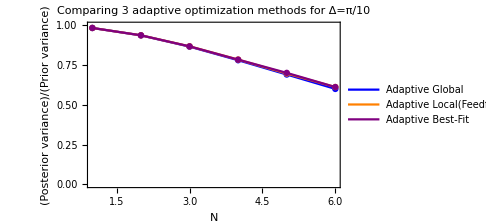

```mathematica
Show[ListPlot[VarRatioGlobalπb10,PlotStyle->Blue],ListLinePlot[VarRatioGlobalπb10,PlotLegends->Placed[{"Adaptive Global"},{0.24,0.6}],PlotStyle->Blue],ListPlot[VarRatioSBSExactπb10,PlotStyle->Orange],ListLinePlot[VarRatioSBSExactπb10,PlotLegends->Placed[{"Adaptive Local(Feedforward)"},{0.35,0.4}],PlotStyle->Orange],ListPlot[VarRatioPluggedExactπb10,PlotStyle->Purple],ListLinePlot[VarRatioPluggedExactπb10,PlotLegends->Placed[{"Adaptive Best-Fit"},{0.25,0.2}],PlotStyle->Purple],AxesLabel-> {"N","VarRatio"},AxesOrigin->{0,0},PlotRange->{{1,6},{0,1}}, Frame->True,FrameLabel->{"N",Style["(Posterior variance)/(Prior variance)",Thick]}, PlotLabel-> "Comparing 3 adaptive optimization methods for Δ=π/10", ImageSize->Medium]
```

#### Δ = 3π/10

```mathematica
VarRatioGlobal3πb10 = {Global21[[2]],Global22[[2]], Global23[[2]],Global24[[2]], Global25[[2]],Global26[[2]]}
VarRatioSBSExact3πb10 = {SBSExact21[[2]],SBSExact22[[2]],SBSExact23[[2]],SBSExact24[[2]],SBSExact25[[2]],SBSExact26[[2]]}
VarRatioPluggedExact3πb10 = {PlugVarianceExact21[[2]],PlugVarianceExact22[[2]],PlugVarianceExact23[[2]],PlugVarianceExact24[[2]],PlugVarianceExact25[[2]],PlugVarianceExact26[[2]]}
```

{0.0641394,0.0443321,0.0288181,0.0208955,0.0176228,0.0156746}

{0.0642602,0.0453213,0.0302358,0.0218529,0.0263785,0.0217545}

{0.0642602,0.0453213,0.0302358,0.0218529,0.0228925,0.0219822}

```mathematica
VarRatioGlobal3πb10 = Table[VarRatioGlobal3πb10[[n]]/((3*π/10)^2/12),{n,1,6}]
VarRatioSBSExact3πb10 =Table[VarRatioSBSExact3πb10[[n]]/((3*π/10)^2/12),{n,1,6}]
VarRatioPluggedExact3πb10 = Table[VarRatioPluggedExact3πb10[[n]]/((3*π/10)^2/12),{n,1,6}]
```

```mathematica
VarRatioGlobal3πb10={0.8664907229357117,0.5989044808431088,0.3893178171156001,0.28228714882069134,0.23807543305993073,0.21175546815372295}
VarRatioSBSExact3πb10={0.8681230275188423,0.6122676497036517,0.4084702770309793,0.29522162267824564,0.35636063264699386,0.29389199944612354}
VarRatioPluggedExact3πb10={0.8681230277246597,0.6122676474515529,0.40847028185531187,0.2952216220989711,0.30926582787131196,0.2969689056401592}
```

{0.866491,0.598904,0.389318,0.282287,0.238075,0.211755}

{0.868123,0.612268,0.40847,0.295222,0.356361,0.293892}

{0.868123,0.612268,0.40847,0.295222,0.309266,0.296969}

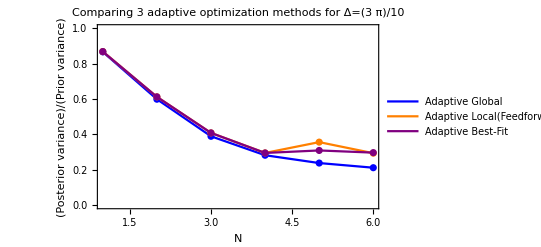

```mathematica
Show[ListPlot[VarRatioGlobal3πb10,PlotStyle->Blue],ListLinePlot[VarRatioGlobal3πb10,PlotLegends->Placed[{"Adaptive Global"},{0.58,0.9}],PlotStyle->Blue],ListPlot[VarRatioSBSExact3πb10,PlotStyle->Orange],ListLinePlot[VarRatioSBSExact3πb10,PlotLegends->Placed[{"Adaptive Local(Feedforward)"},{0.7,0.7}],PlotStyle->Orange],ListPlot[VarRatioPluggedExact3πb10,PlotStyle->Purple],ListLinePlot[VarRatioPluggedExact3πb10,PlotLegends->Placed[{"Adaptive Best-Fit"},{0.6, 0.5}],PlotStyle->Purple],AxesLabel-> {"N","VarRatio"},AxesOrigin->{0,0},PlotRange->{{1,6},{0,1}}, Frame->True,FrameLabel->{"N",Style["(Posterior variance)/(Prior variance)",Thick]}, PlotLabel-> "Comparing 3 adaptive optimization methods for Δ=(3  π)/10"]
```

#### Δ = π/2

```mathematica
VarRatioGlobal5πb10 = {Global21[[3]],Global22[[3]], Global23[[3]],Global24[[3]], Global25[[3]],Global26[[3]]}
VarRatioSBSExact5πb10 = {SBSExact21[[3]],SBSExact22[[3]],SBSExact23[[3]],SBSExact24[[3]],SBSExact25[[3]],SBSExact26[[3]]}
VarRatioPluggedExact5πb10 = {PlugVarianceExact21[[3]],PlugVarianceExact22[[3]],PlugVarianceExact23[[3]],PlugVarianceExact24[[3]],PlugVarianceExact25[[3]],PlugVarianceExact26[[3]]}
```

{0.141553,0.0703001,0.0486302,0.0420686,0.0345499,0.0284223}

{0.143321,0.0739557,0.0920356,0.0491256,0.107981,0.110359}

{0.143321,0.0739557,0.0635963,0.0517979,0.0397187,0.0316001}

```mathematica
VarRatioGlobal5πb10 = Table[VarRatioGlobal5πb10[[n]]/((5*π/10)^2/12),{n,1,6}]
VarRatioSBSExact5πb10 =Table[VarRatioSBSExact5πb10[[n]]/((5*π/10)^2/12),{n,1,6}]
VarRatioPluggedExact5πb10 = Table[VarRatioPluggedExact5πb10[[n]]/((5*π/10)^2/12),{n,1,6}]
```

{0.688433,0.341899,0.236509,0.204597,0.16803,0.138229}

{0.697029,0.359677,0.447608,0.238918,0.525155,0.536721}

{0.697029,0.359677,0.309295,0.251915,0.193168,0.153685}

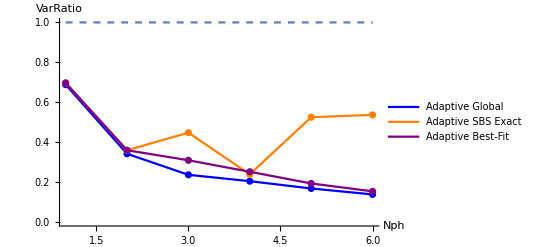

```mathematica
Show[ListPlot[VarRatioGlobal5πb10,PlotStyle->Blue],ListLinePlot[VarRatioGlobal5πb10,PlotLegends->{"Adaptive Global"},PlotStyle->Blue],ListPlot[VarRatioSBSExact5πb10,PlotStyle->Orange],ListLinePlot[VarRatioSBSExact5πb10,PlotLegends->{"Adaptive SBS Exact"},PlotStyle->Orange],ListPlot[VarRatioPluggedExact5πb10,PlotStyle->Purple],ListLinePlot[VarRatioPluggedExact5πb10,PlotLegends->{"Adaptive Best-Fit"},PlotStyle->Purple],ListLinePlot[yequal1,PlotStyle-> Dashed],PlotRange->{0,1} ,AxesLabel-> {"Nph","VarRatio"},AxesOrigin->{0,0}]
```

#### Δ = π

```mathematica
VarRatioGlobalπ= {Global21[[4]],Global22[[4]], Global23[[4]],Global24[[4]], Global25[[4]],Global26[[4]]}
VarRatioSBSExactπ = {SBSExact21[[4]],SBSExact22[[4]],SBSExact23[[4]],SBSExact24[[4]],SBSExact25[[4]],SBSExact26[[4]]}
VarRatioPluggedExactπ = {PlugVarianceExact21[[4]],PlugVarianceExact22[[4]],PlugVarianceExact23[[4]],PlugVarianceExact24[[4]],PlugVarianceExact25[[4]],PlugVarianceExact26[[4]]}
```

{0.281201,0.146697,0.096968,0.0728917,0.0549529,0.0428981}

{0.295823,0.162096,0.485819,0.331947,0.324613,0.337032}

{0.295823,0.160765,0.126692,0.0842614,0.057287,0.0452366}

```mathematica
VarRatioGlobalπ = Table[VarRatioGlobalπ[[n]]/((π)^2/12),{n,1,6}]
VarRatioSBSExactπ =Table[VarRatioSBSExactπ[[n]]/((π)^2/12),{n,1,6}]
VarRatioPluggedExactπ = Table[VarRatioPluggedExactπ[[n]]/((π)^2/12),{n,1,6}]
```

{0.341899,0.178362,0.117899,0.0886257,0.0668148,0.0521579}

{0.359677,0.197085,0.590686,0.403599,0.394682,0.409781}

{0.359677,0.195467,0.154039,0.10245,0.0696526,0.0550011}

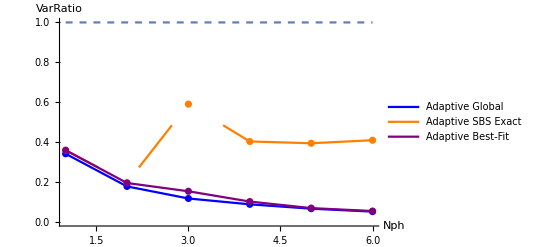

```mathematica
Show[ListPlot[VarRatioGlobalπ,PlotStyle->Blue],ListLinePlot[VarRatioGlobalπ,PlotLegends->{"Adaptive Global"},PlotStyle->Blue],ListPlot[VarRatioSBSExactπ,PlotStyle->Orange],ListLinePlot[VarRatioSBSExactπ,PlotLegends->{"Adaptive SBS Exact"},PlotStyle->Orange],ListPlot[VarRatioPluggedExactπ,PlotStyle->Purple],ListLinePlot[VarRatioPluggedExactπ,PlotLegends->{"Adaptive Best-Fit"},PlotStyle->Purple],ListLinePlot[yequal1,PlotStyle-> Dashed],PlotRange->{0,1} ,AxesLabel-> {"Nph","VarRatio"},AxesOrigin->{0,0}]
```

## Debugging discrepancy between SBS Exact and SBS Best-Fit

### PluggedFeedforward is repeatable

#### Run 1

```mathematica
PluggedFeedforward[3,π]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.126692,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,r0s1→0.422761,r1s1→0.566809,r2s1→0.566809,r3s1→0.422761},{{θ0s1→-0.0672511,θ1s1→1.11972,θ2s1→-1.99277,θ3s1→-4.6699,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→2.46794,θ1s1→-0.112901,θ2s1→-2.35293,θ3s1→-0.103465,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→-0.993519,θ1s1→0.240466,θ2s1→2.12953,θ3s1→-1.5637,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→3.97265,θ1s1→-0.649211,θ2s1→0.273463,θ3s1→5.43371,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)}}},0.0705897}

#### Run 2

```mathematica
PluggedFeedforward[3,π]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.126692,{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,r0s1→0.422761,r1s1→0.566809,r2s1→0.566809,r3s1→0.422761},{{θ0s1→-0.0270497,θ1s1→-1.62727,θ2s1→-5.83354,θ3s1→-4.6297,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→-3.06721,θ1s1→1.35494,θ2s1→0.657214,θ3s1→-5.63862,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→0.597829,θ1s1→1.08522,θ2s1→0.69737,θ3s1→0.0276452,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)},{θ0s1→4.10466,θ1s1→3.24714,θ2s1→5.21498,θ3s1→5.56572,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→1/(√2)}}},0.0705897}

### Feedforward is not repeatable, checking all steps for 2 runs - Degeneracy exists, Approx method is repeatable

#### Run 1

```mathematica
Feedforward[3,π]
```

Δ

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.312554,{{θ0s1→4.27276,θ1s1→2.70197,θ2s1→1.13117,θ3s1→-3.58122,r0s1→0.429711,r1s1→0.561559,r2s1→0.561559,r3s1→0.429711},{{θ0s1→1.05485,θ1s1→3.14675,θ2s1→2.09705,θ3s1→-2.09423,r0s1→0.453378,r1s1→0.542631,r2s1→0.542631,r3s1→0.453378},{θ0s1→3.56718,θ1s1→-1.33108,θ2s1→0.0538545,θ3s1→-4.8444,r0s1→0.431819,r1s1→0.559939,r2s1→0.559939,r3s1→0.431819},{θ0s1→11.4834,θ1s1→-8.75108,θ2s1→5.57195,θ3s1→-8.37935,r0s1→0.431819,r1s1→0.559939,r2s1→0.559939,r3s1→0.431819},{θ0s1→2.22197,θ1s1→0.130066,θ2s1→-1.96183,θ3s1→-4.05373,r0s1→0.453378,r1s1→0.542631,r2s1→0.542631,r3s1→0.453378}}},0.161461}

```mathematica
VarOptPrior1Shot
```

{0.191083,{θ0s1→1.2212,θ1s1→2.79199,θ2s1→-1.92039,θ3s1→2.79199,r0s1→0.429711,r1s1→0.561559,r2s1→0.561559,r3s1→0.429711}}

```mathematica
VarFeedforward1
```

{0.550919,0.787922,0.787921,0.550919}

```mathematica
OptStatePrior1Shot
```

{θ0s1→4.27276,θ1s1→2.70197,θ2s1→1.13117,θ3s1→-3.58122,r0s1→0.429711,r1s1→0.561559,r2s1→0.561559,r3s1→0.429711}

```mathematica
OptStatePrior1Shot2={θ0s1->3.390444467303787,θ1s1->-1.32194455035896,θ2s1->0.2488517074858555,θ3s1->4.961240621979311,r0s1->0.4297114160894566,r1s1->0.5615586431446404,r2s1->0.5615586479190741,r3s1->0.42971138469820136}
```

{θ0s1→3.39044,θ1s1→-1.32194,θ2s1→0.248852,θ3s1→4.96124,r0s1→0.429711,r1s1→0.561559,r2s1→0.561559,r3s1→0.429711}

```mathematica
Chop[listOfPmϕ1/.{ϕ->0.123}]
```

{0.328342,0.157703,0.276949,0.237006}

```mathematica
Chop[listOfPmϕ/.OptStatePrior1Shot2/.{ϕ->0.123}]
```

{0.237006,0.276949,0.157703,0.328342}

```mathematica
VffExact
```

0.138583

```mathematica
VarFeedforward
```

0.161461

```mathematica
(*We can see that there exists degeneracy in the states. There are multiple states which minimize the variance*)
```